```mathematica
$Assumptions={sp>0,s>0,sp+q2>0,t1>0,m2>0,q2<0,s4>0,
0<ρ,ρ<1,0<β,β<1,0<χ,χ<1,
ρq<0,βq>1,0<χq<1,
0<ρp,ρp<ρq/(ρq-1),ρp<ρ,ρp<1,ρp ρq/(ρq+ρp)>0,ρ ρq/(ρq-ρ)>0,
0<βp,βp<1,0<χp,χq<χp,χp<1,β<βp,χ>χp,
δ>0
}/.List->And
```

sp>0&&s>0&&q2+sp>0&&t1>0&&m2>0&&q2<0&&s4>0&&0<ρ&&ρ<1&&0<β&&β<1&&0<χ&&χ<1&&ρq<0&&βq>1&&0<χq<1&&0<ρp&&ρp<ρq/(-1+ρq)&&ρp<ρ&&ρp<1&&(ρp ρq)/(ρp+ρq)>0&&(ρ ρq)/(-ρ+ρq)>0&&0<βp&&βp<1&&0<χp&&χq<χp&&χp<1&&β<βp&&χ>χp&&δ>0

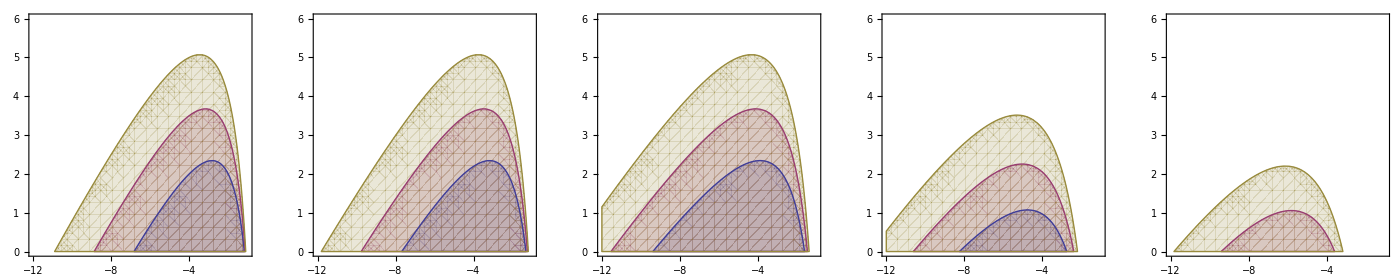

```mathematica
Module[{norm,t1min,t1max,s4min,s4max,f,g},
norm={β-> Sqrt[1-ρ],ρ-> 4m2/s,sp-> s-q2};
t1min=-sp/2(1+β);
t1max=-sp/2(1-β);
s4min=0;
s4max=s/(sp t1)(t1-t1min)(t1-t1max);
f=(t1min<t1 && t1<t1max)&&(s4min<s4 && s4<s4max)//.norm;
g[m2V_,q2V_,sV_]:=f//.{m2-> m2V,s-> sV,q2-> q2V};
Show[GraphicsRow[{
RegionPlot[{g[1,0,8],g[1,0,10],g[1,0,12]},{t1,-12,-1},{s4,0,6}],
RegionPlot[{g[1,-1,8],g[1,-1,10],g[1,-1,12]},{t1,-12,-1},{s4,0,6}],
RegionPlot[{g[1,-3,8],g[1,-3,10],g[1,-3,12]},{t1,-12,-1},{s4,0,6}],
RegionPlot[{g[3/2,-3,8],g[3/2,-3,10],g[3/2,-3,12]},{t1,-12,-1},{s4,0,6}],
RegionPlot[{g[2,-3,8],g[2,-3,10],g[2,-3,12]},{t1,-12,-1},{s4,0,6}]
}],ImageSize-> 1400]
]
```

## A2L

### psLog3a

#### calculate

```mathematica
IntIntAL2[psLog3a][raw]={-1/(sp^2 (sp+t1+u1) (-4 q2 (m2+t1)+(-q2+sp+u1)^2)^(5/2))
4 π q2 (m2+sp+t1+u1) (16 m2^3 q2 (4 q2-sp)+q2^4 (-sp+t1)-(sp+u1) (2 sp^4+sp (sp-2 t1) (5 sp+2 t1) u1+2 (2 sp^2-5 sp t1+t1^2) u1^2+(sp-2 t1) u1^3)+q2^3 (5 sp^2-5 t1 (2 t1+u1)+sp (3 t1+4 u1))+q2^2 (-9 sp^3-sp^2 (7 t1+15 u1)+sp (20 t1^2+6 t1 u1-6 u1^2)+t1 (30 t1^2+28 t1 u1+9 u1^2))+q2 (7 sp^4+3 sp^3 (t1+6 u1)+t1 u1 (2 t1^2-16 t1 u1-7 u1^2)+sp^2 (-18 t1^2-11 t1 u1+15 u1^2)-sp (6 t1^3+40 t1^2 u1+21 t1 u1^2-4 u1^3))+2 m2 (2 q2^4-q2^3 (6 sp+23 t1+8 u1)+q2^2 (8 sp^2+49 sp t1+70 t1^2+21 sp u1+47 t1 u1+12 u1^2)+(sp+u1) (sp^3+2 sp (3 sp+t1) u1+(7 sp-t1) u1^2+2 u1^3)-q2 (sp (5 sp+2 t1) (sp+6 t1)+(21 sp^2+60 sp t1-8 t1^2) u1+(24 sp+23 t1) u1^2+8 u1^3))+4 m2^2 (-8 q2^3+sp (sp+u1)^2+q2^2 (17 sp+42 t1+16 u1)-q2 (11 sp^2-2 (t1-4 u1) u1+10 sp (t1+2 u1)))),
(-2 m2 q2+(sp+t1+u1) (-q2+sp+u1-Sqrt[-4 m2 q2+q2^2+(sp+u1)^2-2 q2 (sp+2 t1+u1)]))/(-2 m2 q2+(sp+t1+u1) (-q2+sp+u1+Sqrt[-4 m2 q2+q2^2+(sp+u1)^2-2 q2 (sp+2 t1+u1)]))};
Module[{c,l,psN},
{c,l}=IntIntAL2[psLog3a][raw];
psN=(1/(2π) (*Kqγ NC CF*) (s4/(s4+m2)));
c=FullSimplify[psN c (m2(*/(4π)*)) 1/sp^2/.{u1-> s4-sp-t1}];
l=FullSimplify[l/.{u1-> s4-sp-t1}];
IntIntAL2[psLog3a][coeffs]={c,l}
]
```

{-1/(sp^4 (-4 q2 (m2+t1)+(q2-s4+t1)^2)^(5/2))2 m2 q2 (16 m2^3 q2 (4 q2-sp)-(q2-s4)^3 (q2-s4-sp) sp+(q2-s4) ((q2-2 s4) (q2-s4)^2+4 (q2-s4) (q2+2 s4) sp-(q2-3 s4) sp^2) t1-(5 (q2-2 s4) (q2-s4) (q2+s4)+2 (q2^2-2 q2 s4+5 s4^2) sp+(q2-3 s4) sp^2) t1^2+(11 q2^2+13 q2 s4+18 s4^2-4 q2 sp+sp^2) t1^3+(-11 q2-14 s4+3 sp) t1^4+4 t1^5+2 m2 ((q2-s4) (2 (q2-s4)^3+(q2-s4) (2 q2+s4) sp-(q2-2 s4) sp^2)+(-15 q2^3+q2^2 (23 s4+5 sp)+s4 (-9 s4^2+s4 sp+sp^2)+q2 (s4^2-14 s4 sp+2 sp^2)) t1+(35 q2^2+30 q2 s4+15 s4^2-6 q2 sp-5 s4 sp+sp^2) t1^2+(-23 q2-11 s4+3 sp) t1^3+3 t1^4)-4 m2^2 (8 q2^3-sp (s4-t1)^2-q2^2 (16 s4+sp+26 t1)+q2 (8 s4^2+4 s4 sp-sp^2-18 s4 t1+8 sp t1+10 t1^2))),(2 m2 q2+s4 (q2-s4+t1+√(-4 m2 q2+(q2-s4)^2-2 (q2+s4) t1+t1^2)))/(2 m2 q2+s4 (q2-s4+t1-√(-4 m2 q2+(q2-s4)^2-2 (q2+s4) t1+t1^2)))}

#### check

```mathematica
Module[{norm,num,ana,cmp},
norm={
χ-> (1-β)/(1+β),χp-> (1-βp)/(1+βp),χq-> (β-1)/(βq+1),
β->Sqrt[1-ρ],βp->Sqrt[1-ρp],βq->Sqrt[1-ρq],
ρ-> 4m2/s,ρp-> 4m2/sp,ρq-> 4m2/q2,
sp-> s-q2};
num[p_]:=Module[{c,l,f,s4min,s4max,t1min,t1max,jacs4,jact1},
{c,l}=IntIntAL2[psLog3a][coeffs];
f=(c*Log[l])//.norm//.p;
s4min=0;
s4max=s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2)//.norm//.p;
jacs4=s4max-s4min;
t1min=-sp/2(1+β)//.norm//.p;
t1max=-sp/2(1-β)//.norm//.p;
jact1=t1max-t1min;
(*Print[f," 0 < s4 < ",s4max, " und ",t1min," < t1 < ",t1max];*)
NIntegrate[f*jact1*jacs4/.{s4-> s4min+jacs4*a}/.{t1-> t1min+jact1*b},{a,0,1},{b,0,1}(*,Method-> "AdaptiveMonteCarlo"*)]
];
ana[p_]:=Module[{u1,u2,l},
l=IntIntAL2[psLog3a][JlowerRes];
u1=IntIntAL2[psLog3a][Jupper1Res];
u2=IntIntAL2[psLog3a][Jupper2Res];
(*u2=Take[u2,3];*)
{u1,u2,l}={u1,u2,l}//.norm/.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]}//.p;
Print[N@{u1,u2,l}];
u2-u1+l
];
cmp[p_]:=Module[{a,n},
n=num[p];
a=0.(*N@ana[p]*);
Print["a = ",a,", n = ",n, " => diff = ",a-n, ", rel. err = ",(n-a)/n]
];
cmp[{m2->1,q2->-1,s-> 5}];
(*c[{m2->1,q2->-10,s-> 5}];
c[{m2->1,q2->-1,s-> 400}];
c[{m2->1,q2->-10,s-> 400}];
c[{m2->5,q2->-10,s-> 400}];
c[{m2->50,q2->-100,s-> 400}];
c[{m2->500,q2->-10,s-> 4000}];*)
Do[cmp[{m2->1,q2->-1,s-> (5+10^sV)}],{sV,0,2,.1}];
Do[cmp[{m2->1,q2->-1-10^qV,s-> 20}],{qV,0,2,.1}]
]
```

a = 0., n = 0.000695495 => diff = -0.000695495, rel. err = 1.

a = 0., n = 0.00244422 => diff = -0.00244422, rel. err = 1.

a = 0., n = 0.00293896 => diff = -0.00293896, rel. err = 1.

a = 0., n = 0.00354996 => diff = -0.00354996, rel. err = 1.

a = 0., n = 0.00428007 => diff = -0.00428007, rel. err = 1.

a = 0., n = 0.00511324 => diff = -0.00511324, rel. err = 1.

a = 0., n = 0.006006 => diff = -0.006006, rel. err = 1.

a = 0., n = 0.00688326 => diff = -0.00688326, rel. err = 1.

a = 0., n = 0.00764363 => diff = -0.00764363, rel. err = 1.

a = 0., n = 0.00817712 => diff = -0.00817712, rel. err = 1.

a = 0., n = 0.00839224 => diff = -0.00839224, rel. err = 1.

a = 0., n = 0.00824284 => diff = -0.00824284, rel. err = 1.

a = 0., n = 0.00774284 => diff = -0.00774284, rel. err = 1.

a = 0., n = 0.00696194 => diff = -0.00696194, rel. err = 1.

a = 0., n = 0.00600478 => diff = -0.00600478, rel. err = 1.

a = 0., n = 0.00498336 => diff = -0.00498336, rel. err = 1.

a = 0., n = 0.00399364 => diff = -0.00399364, rel. err = 1.

a = 0., n = 0.00310242 => diff = -0.00310242, rel. err = 1.

a = 0., n = 0.0023452 => diff = -0.0023452, rel. err = 1.

a = 0., n = 0.00173136 => diff = -0.00173136, rel. err = 1.

a = 0., n = 0.00125251 => diff = -0.00125251, rel. err = 1.

a = 0., n = 0.000890562 => diff = -0.000890562, rel. err = 1.

a = 0., n = 0.0110047 => diff = -0.0110047, rel. err = 1.

a = 0., n = 0.0117665 => diff = -0.0117665, rel. err = 1.

a = 0., n = 0.0126252 => diff = -0.0126252, rel. err = 1.

a = 0., n = 0.0135686 => diff = -0.0135686, rel. err = 1.

a = 0., n = 0.0145713 => diff = -0.0145713, rel. err = 1.

a = 0., n = 0.0155905 => diff = -0.0155905, rel. err = 1.

a = 0., n = 0.0165626 => diff = -0.0165626, rel. err = 1.

a = 0., n = 0.0174024 => diff = -0.0174024, rel. err = 1.

a = 0., n = 0.0180069 => diff = -0.0180069, rel. err = 1.

a = 0., n = 0.0182661 => diff = -0.0182661, rel. err = 1.

a = 0., n = 0.0180817 => diff = -0.0180817, rel. err = 1.

a = 0., n = 0.0173914 => diff = -0.0173914, rel. err = 1.

a = 0., n = 0.0161918 => diff = -0.0161918, rel. err = 1.

a = 0., n = 0.0145502 => diff = -0.0145502, rel. err = 1.

a = 0., n = 0.0125978 => diff = -0.0125978, rel. err = 1.

a = 0., n = 0.0105044 => diff = -0.0105044, rel. err = 1.

a = 0., n = 0.00844186 => diff = -0.00844186, rel. err = 1.

a = 0., n = 0.00655116 => diff = -0.00655116, rel. err = 1.

a = 0., n = 0.00492273 => diff = -0.00492273, rel. err = 1.

a = 0., n = 0.00359366 => diff = -0.00359366, rel. err = 1.

a = 0., n = 0.00255774 => diff = -0.00255774, rel. err = 1.

### psLog3b

#### calculate

```mathematica
IntIntAL2[psLog3b][raw]={((4 π q2 (m2+sp+t1+u1) (-4 m2^2 (4 q2+5 sp)+(q2-t1-u1) (q2 (-sp+t1)+sp u1-2 t1 (t1+u1))+2 m2 (2 q2^2+sp^2+q2 (2 sp-7 t1-4 u1)-sp (3 t1+u1)+(t1+u1) (3 t1+2 u1))))/(sp^2 (sp+t1+u1) (-4 m2 (q2+sp)+(-q2+t1+u1)^2)^(3/2))),
(2 m2 (q2+sp)+(sp+t1+u1) (q2-t1-u1+Sqrt[-4 m2 (q2+sp)+(-q2+t1+u1)^2]))/(2 m2 (q2+sp)-(sp+t1+u1) (-q2+t1+u1+Sqrt[-4 m2 (q2+sp)+(-q2+t1+u1)^2]))};
Module[{c,l,psN},
{c,l}=IntIntAL2[psLog3b][raw];
psN=(1/(2π) (*Kqγ NC CF*) (s4/(s4+m2)));
c=FullSimplify[psN c (m2(*/(4π)*)) 1/sp^2/.{u1-> s4-sp-t1}/.{sp-> s-q2}];
l=FullSimplify[l/.{u1-> s4-sp-t1}/.{sp-> s-q2}];
IntIntAL2[psLog3b][coeffs]={c,l}
]
```

{(2 m2 q2 (4 m2^2 (q2-5 s)+(s-s4) ((q2-s) (s-s4)+(s-2 s4) t1)+2 m2 (4 s^2-5 s s4+2 s4^2+q2 (-2 s+s4)-3 s t1+s4 t1)))/((q2-s)^4 (-4 m2 s+(s-s4)^2)^(3/2)),(2 m2 s+(s+√(-4 m2 s+(s-s4)^2)-s4) s4)/(2 m2 s-s4 (-s+√(-4 m2 s+(s-s4)^2)+s4))}

```mathematica
Module[{s4max,norm,p,t1min,t1max,wmin},
norm={sp-> s-q2,β-> Sqrt[1-ρ],ρ->4m2/s};
s4max=s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2);
Print@FullSimplify[s4max-s-t1/.{β->Sqrt[1-ρ]}]
]
```

(-1+s/sp) t1+(s sp ρ)/(4 t1)

```mathematica
Solve[{s4==s(1-(1+w^2)/(2w) Sqrt@ρ)},w]//FullSimplify
```

{{w→(s-s4-√((s-s4)^2-s^2 ρ))/(s √ρ)},{w→(s-s4+√((s-s4)^2-s^2 ρ))/(s √ρ)}}

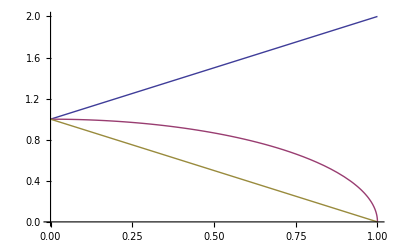

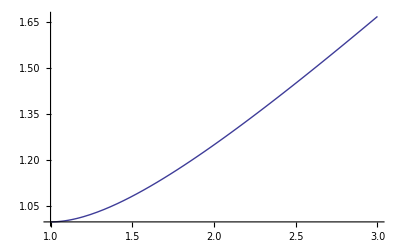

```mathematica
Plot[{(1+β),Sqrt[1-β^2],(1-β)},{β,0,1}]
Plot[(1+w^2)/(2w),{w,1,3}]
```

```mathematica
Module[{c,l,Ts4,Tt1,iTt1,iTs4,jac,t,t1min,vmin,t1max,vmax,s4min,wmin,s4max,wmax,wmin1,wmin2,I,Ilower1,Ilower2,Iupper},
{c,l}=IntIntAL2[psLog3b][coeffs];
Tt1=-sp/2v;
Ts4= s(1-(1+(w)^2)/(2(w))Sqrt@ρ);
t={q2-> 4m2/ρq,sp-> 4m2/ρp,s-> 4m2/ρ,s4->Ts4,t1-> Tt1};
t=Map[First@#-> (Last@#//.t)&,t];
Print@t;
iTt1=Solve[{t1==Tt1},v]//FullSimplify;
Print@iTt1;
iTs4=Solve[{s4==Ts4},w]//FullSimplify;
Print@iTs4;

t1min=-sp/2(1+β);
vmax=FullSimplify[(v/.Last@iTt1/.{t1-> t1min})/.t];
t1max=-sp/2(1-β);
vmin=FullSimplify[(v/.Last@iTt1/.{t1-> t1max})/.t];
Print["vmin = ",vmin,", vmax = ",vmax];

s4min=0;
wmax=FullSimplify[FullSimplify[(w/.Last@iTs4/.{s4-> s4min})/.t]/.{ρ-> 1-β^2}/.{β-> (1-χ)/(1+χ)}];
s4max=s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2);
wmin=FullSimplify[FullSimplify[(w/.Last@iTs4/.{s4-> s4max})/.t]/.{β^2-> 1-ρ},Assumptions-> {v>0,ρ>0}];
wmin1=Refine[wmin,v<Sqrt[ρ]&&v>0];
wmin2=Refine[wmin,v≥ Sqrt@ρ];
Print["wmin = ",wmin," => ",{wmin1,wmin2}," => ",
FullSimplify[wmin1/.{v-> vmin}/.{ρ-> 1-β^2}/.{β-> (1-χ)/(1+χ)}]," > wmin1 > ",(wmin1/.{v-> Sqrt@ρ})," and ",
(wmin2/.{v-> Sqrt@ρ})," < wmin2 < ",FullSimplify[wmin2/.{v->vmax}/.{ρ-> 1-β^2}/.{β-> (1-χ)/(1+χ)}],", wmax = ",wmax
];

jac=(D[Ts4,w]) * (D[Tt1,v]);

{c,l}=FullSimplify[FullSimplify[{c jac,l}/.{sp-> s-q2}/.t,Assumptions-> {m2>0,1>ρ,ρ>0}]/.{ρ-ρq-> -ρ ρq/ρp},Assumptions-> {w>1}];
Print@{c,l};
I=Integrate[c  Log@l,w,Assumptions-> {w>1}];
I=Collect[I,{Log[_],PolyLog[_,_]},(FullSimplify[#,Assumptions-> {w>1}])&];
I=I/.{Log[z_]:> ln[Simplify@Together@z],PolyLog[2,z_]:> Li2[Simplify@Together@z]};
I=I/.{ln[1-w^2]-> ln[w^2-1]+ln[-1],ln[1-w]-> ln[w-1]+ln[-1],ln[-2w+Sqrt@ρ]-> ln[2w-Sqrt@ρ]+ln[-1]};
I=Collect[I,{ln[_],Li2[_]},FullSimplify];
I=FullSimplify@I;
I=I/.{ln[a_]+ln@b_:> ln@FullSimplify[a b]}/.{ln[a_]-ln@b_:> ln@FullSimplify[a/b]};
I=I//.{3*ln[w] + ln[(1 - (2*w)/Sqrt[ρ])/w^3] - ln[w - Sqrt[ρ]/2]-> ln[Simplify@Together[w^3*((1 - (2*w)/Sqrt[ρ])/w^3)/(w - Sqrt[ρ]/2)]],ln[w-Sqrt[ρ]/2]-> ln[2w-Sqrt@ρ]-ln[2],ln[-(2/Sqrt[ρ])]-> ln[(2/Sqrt[ρ])]+ln[-1]};
I=Collect[I,{ln[_],Li2[_]},FullSimplify];
I=I/.{1/(Sqrt@ρ-2)-> (Sqrt@ρ+2)/(ρ-4),1/(Sqrt@ρ+2)-> (Sqrt@ρ-2)/(ρ-4)};
I=I/.{ln[w-1]-> ln[w^2-1]-ln[w+1]};
I=Collect[I,{ln[_],Li2[_]},FullSimplify];
Print@I;

Ilower1=I/.{w-> wmin1};
Ilower1=FullSimplify[Ilower1,Assumptions-> {v<Sqrt[ρ]&&v>1-β}];
Ilower2=I/.{w-> wmin2};
Ilower2=FullSimplify[Ilower2,Assumptions-> {v≥ Sqrt@ρ,v<1+β}];
Iupper=I/.{w-> wmax};
Iupper=FullSimplify[Iupper/.{Sqrt[ρ χ]-> (1-β),Sqrt[ρ/χ]-> (1+β)}];
IntIntAL2[psLog3b][Is]={Ilower1,Ilower2,Iupper}
]
```

{q2→(4 m2)/ρq,sp→(4 m2)/ρp,s→(4 m2)/ρ,s4→(4 m2 (1-((1+w^2) √ρ)/(2 w)))/ρ,t1→-(2 m2 v)/ρp}

{{v→-(2 t1)/sp}}

{{w→(s-s4-√((s-s4)^2-s^2 ρ))/(s √ρ)},{w→(s-s4+√((s-s4)^2-s^2 ρ))/(s √ρ)}}

vmin = 1-β, vmax = 1+β

wmin = Piecewise[{{v/(√ρ), v^2≥ρ}, {(√ρ)/v, True}}] => {(√ρ)/v,v/(√ρ)} => 1/(√χ) > wmin1 > 1 and 1 < wmin2 < 1/(√χ), wmax = 1/(√χ)

{(ρp^2 (2 w^2 ρ^2 ρp-2 (1+w^4) ρp ρq+2 w (1+w^2) √ρ (v+ρp) ρq-(w+w^3) ρ^(3/2) (2 ρp-v ρq)+2 ρ (-v (1+w^4) ρq+ρp (1+ρq-3 w^2 ρq+w^4 (1+ρq)))))/(8 w (-1+w^2)^2 ρ ρq^2),w^4+(2 (-w^3+w^5))/(-2 w+√ρ)}

(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Li2[1-(2 w)/(√ρ)])/(4 ρ ρq^2)+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Li2[(w √ρ)/2])/(4 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[-1]^2)/(8 ρ ρq^2)+(3 ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) ln[w]^2)/(8 ρ ρq^2)+ln[w] ((ρp^2 (-(6 (2+ρ) ρp (ρ-ρq))/ρ+12 v ρq))/(16 ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[w^3])/(4 ρ ρq^2))+(ρp^2 ((-6+ρ) ρ ρp+4 v ρq-(v (-2+ρ) ρ+(-6+ρ) ρp) ρq) ln[1+w])/(2 (-4+ρ) √ρ ρq^2)+((-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) ln[-1+w^2])/(4 (-2+√ρ) ρ ρq^2)-(ρp^2 (2 ρ ρp+ρ^2 ρp-2 ρp ρq+2 w √ρ (v+ρp) ρq-ρ (2 v+ρp) ρq+w ρ^(3/2) (-2 ρp+v ρq)) ln[w^3 (w+(2 (-1+w^2))/(-2 w+√ρ))])/(8 (-1+w^2) ρ ρq^2)-(ρp^2 ((-2+ρ) ρp (ρ-ρq)+4 v ρq) ln[2-w √ρ])/(8 (-4+ρ) ρq^2)+ln[-1] ((ρp^2 (3 ρ^(5/2) ρp-16 ρp ρq+2 √ρ (4 v+ρp) ρq+ρ^2 (2 ρp+3 v ρq)-2 ρ (ρp (-8+ρq)+5 v ρq)-ρ^(3/2) (2 v ρq+ρp (2+3 ρq))))/(16 (2+√ρ) ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[2/(√ρ)])/(8 ρ ρq^2))+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[2] ln[(2 w)/(√ρ)])/(4 ρ ρq^2)+ln[2 w-√ρ] (-(ρp^2 (4 ρ ρp-2 v ρ ρq+v ρ^2 ρq-4 ρp ρq))/(4 (-4+ρ) ρ ρq^2)+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) ln[(2 w)/(√ρ)])/(4 ρ ρq^2))

{1/(16 ρq^2)ρp^2 ((4 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Li2[(-2+v)/v])/ρ+(4 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Li2[ρ/(2 v)])/ρ+(2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[-1]^2)/ρ+(4 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[2] ln[2/v])/ρ+(8 ((-6+ρ) ρ ρp+4 v ρq-(v (-2+ρ) ρ+(-6+ρ) ρp) ρq) ln[(v+√ρ)/v])/((-4+ρ) √ρ)+(ln[-1] (3 ρ^(5/2) ρp-16 ρp ρq+2 √ρ (4 v+ρp) ρq+ρ^2 (2 ρp+3 v ρq)-2 ρ (ρp (-8+ρq)+5 v ρq)-ρ^(3/2) (2 ρp+2 v ρq+3 ρp ρq)+2 (2+√ρ) (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[2/(√ρ)]))/((2+√ρ) ρ)+(6 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) ln[(√ρ)/v]^2)/ρ-(4 (4 ρ ρp-2 v ρ ρq+v ρ^2 ρq-4 ρp ρq+(-4+ρ) (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[2/v]) ln[-((-2+v) √ρ)/v])/((-4+ρ) ρ)+(2 ln[(√ρ)/v] (-3 ρ (2+ρ) ρp+3 (2 v ρ+(2+ρ) ρp) ρq+2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[ρ^(3/2)/v^3]))/ρ+(2 v (-2 v^2 ρ ρq+2 ρ ρp (-ρ+ρq)+v (2+ρ) (-ρp ρq+ρ (ρp+ρq))) ln[(ρ (-2 v+ρ))/((-2+v) v^3)])/((v^2-ρ) ρ)+(4 (-2+4 √ρ-3 ρ+ρ^(3/2)) (ρ ρp+v √ρ ρq-ρp ρq) ln[-1+ρ/v^2])/((-2+√ρ) ρ)-(2 ((-2+ρ) ρp (ρ-ρq)+4 v ρq) ln[2-ρ/v])/(-4+ρ)),1/(16 ρq^2)ρp^2 ((4 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Li2[v/2])/ρ+(4 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Li2[1-(2 v)/ρ])/ρ+(2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[-1]^2)/ρ-(2 ((-2+ρ) ρp (ρ-ρq)+4 v ρq) ln[2-v])/(-4+ρ)+(4 (-2+4 √ρ-3 ρ+ρ^(3/2)) (ρ ρp+v √ρ ρq-ρp ρq) ln[-1+v^2/ρ])/((-2+√ρ) ρ)+(8 ((-6+ρ) ρ ρp+4 v ρq-(v (-2+ρ) ρ+(-6+ρ) ρp) ρq) ln[1+v/(√ρ)])/((-4+ρ) √ρ)+(4 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[2] ln[(2 v)/ρ])/ρ+(ln[-1] (3 ρ^(5/2) ρp-16 ρp ρq+2 √ρ (4 v+ρp) ρq+ρ^2 (2 ρp+3 v ρq)-2 ρ (ρp (-8+ρq)+5 v ρq)-ρ^(3/2) (2 ρp+2 v ρq+3 ρp ρq)+2 (2+√ρ) (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[2/(√ρ)]))/((2+√ρ) ρ)+(2 (-3 ρ (2+ρ) ρp+3 (2 v ρ+(2+ρ) ρp) ρq+2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[v^3/ρ^(3/2)]) ln[v/(√ρ)])/ρ+(6 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) ln[v/(√ρ)]^2)/ρ-(4 (4 ρ ρp-2 v ρ ρq+v ρ^2 ρq-4 ρp ρq+(-4+ρ) (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[(2 v)/ρ]) ln[(2 v-ρ)/(√ρ)])/((-4+ρ) ρ)-(2 (ρ (2-2 v+ρ) ρp+(v^2 (2+ρ)-(2+ρ) ρp+2 v (-ρ+ρp)) ρq) ln[((-2+v) v^3)/(ρ (-2 v+ρ))])/(v^2-ρ)),1/(16 ρq^2)ρp^2 ((4 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Li2[(√(ρ/χ))/2])/ρ+(4 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Li2[1-2/(√(ρ χ))])/ρ+(2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[-1]^2)/ρ+(ln[-1] (3 ρ^(5/2) ρp-16 ρp ρq+2 √ρ (4 v+ρp) ρq+ρ^2 (2 ρp+3 v ρq)-2 ρ (ρp (-8+ρq)+5 v ρq)-ρ^(3/2) (2 ρp+2 v ρq+3 ρp ρq)+2 (2+√ρ) (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[2/(√ρ)]))/((2+√ρ) ρ)-(2 ((-2+ρ) ρp (ρ-ρq)+4 v ρq) ln[2-√(ρ/χ)])/(-4+ρ)+(4 (-2+4 √ρ-3 ρ+ρ^(3/2)) (ρ ρp+v √ρ ρq-ρp ρq) ln[-1+1/χ])/((-2+√ρ) ρ)+(8 ((-6+ρ) ρ ρp+4 v ρq-(v (-2+ρ) ρ+(-6+ρ) ρp) ρq) ln[1+1/(√χ)])/((-4+ρ) √ρ)+(2 (-3 ρ (2+ρ) ρp+3 (2 v ρ+(2+ρ) ρp) ρq+2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[1/χ^(3/2)]) ln[1/(√χ)])/ρ+(6 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) ln[1/(√χ)]^2)/ρ+(4 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[2] ln[2/(√(ρ χ))])/ρ-(4 ln[-√ρ+2/(√χ)] (4 ρ ρp-2 v ρ ρq+v ρ^2 ρq-4 ρp ρq+(-4+ρ) (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[2/(√(ρ χ))]))/((-4+ρ) ρ)+(2 (√ρ (2 (v+ρp) ρq+ρ (-2 ρp+v ρq))+(ρ (2+ρ) ρp-(2 v ρ+(2+ρ) ρp) ρq) √χ) √χ ln[(√ρ-2 √χ)/(-2 χ^(3/2)+√ρ χ^2)])/(ρ (-1+χ)))}

```mathematica
Module[{Ilower1,Ilower2,Iupper,I1},
{Ilower1,Ilower2,Iupper}=IntIntAL2[psLog3b][Is];
I1=Ilower1-Iupper;
I1=Collect[I1,{ln@_,Li2@_},FullSimplify];
I1=I1/.{ln[-Sqrt[ρ] + 2/Sqrt[χ]]-> ln[2-Sqrt[ρ χ]]-1/2ln@χ}//.{Sqrt[ρ χ]-> (1-β),1/Sqrt[ρ χ]-> 1/(1-β),Sqrt[ρ/χ]-> (1+β)};
I1=I1/.{ln[1/Sqrt@χ]-> -1/2ln@χ,ln[1/χ^(3/2)]-> -3/2ln[χ]};
I1=Collect[I1,{ln@_,Li2@_},FullSimplify];
IntIntAL2[psLog3b][Ilow]=I1
]
```

(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Li2[(-2+v)/v])/(4 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Li2[1-2/(1-β)])/(4 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Li2[(1+β)/2])/(4 ρ ρq^2)+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Li2[ρ/(2 v)])/(4 ρ ρq^2)+ln[2] ((ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[2/v])/(4 ρ ρq^2)+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) ln[2/(1-β)])/(4 ρ ρq^2))+(ρp^2 ((-2+ρ) ρp (ρ-ρq)+4 v ρq) ln[1-β])/(8 (-4+ρ) ρq^2)+(ρp^2 (4 ρ ρp-2 v ρ ρq+v ρ^2 ρq-4 ρp ρq) ln[1+β])/(4 (-4+ρ) ρ ρq^2)+(ρp^2 ((-6+ρ) ρ ρp+4 v ρq-(v (-2+ρ) ρ+(-6+ρ) ρp) ρq) ln[(v+√ρ)/v])/(2 (-4+ρ) √ρ ρq^2)+(3 ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) ln[(√ρ)/v]^2)/(8 ρ ρq^2)-(ρp^2 (4 ρ ρp-2 v ρ ρq+v ρ^2 ρq-4 ρp ρq) ln[-((-2+v) √ρ)/v])/(4 (-4+ρ) ρ ρq^2)+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) ln[2/v] ln[-((-2+v) √ρ)/v])/(4 ρ ρq^2)+ln[(√ρ)/v] ((3 ρp^2 (-ρ (2+ρ) ρp+(2 v ρ+(2+ρ) ρp) ρq))/(8 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[ρ^(3/2)/v^3])/(4 ρ ρq^2))+(v ρp^2 (-2 v^2 ρ ρq+2 ρ ρp (-ρ+ρq)+v (2+ρ) (-ρp ρq+ρ (ρp+ρq))) ln[(ρ (-2 v+ρ))/((-2+v) v^3)])/(8 (v^2-ρ) ρ ρq^2)+((-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) ln[-1+ρ/v^2])/(4 (-2+√ρ) ρ ρq^2)-(ρp^2 ((-2+ρ) ρp (ρ-ρq)+4 v ρq) ln[2-ρ/v])/(8 (-4+ρ) ρq^2)-((-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) ln[-1+1/χ])/(4 (-2+√ρ) ρ ρq^2)+(ρp^2 (-(-6+ρ) ρ ρp+(v (-4+(-2+ρ) ρ)+(-6+ρ) ρp) ρq) ln[1+1/(√χ)])/(2 (-4+ρ) √ρ ρq^2)-(ρp^2 (3 ρ^3 ρp+16 ρp ρq-ρ^2 (4 v ρq+3 ρp (2+ρq))+2 ρ (10 v ρq+ρp (-8+3 ρq))) ln[χ])/(16 (-4+ρ) ρ ρq^2)+(3 ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) ln[χ]^2)/(32 ρ ρq^2)+ln[2/(1-β)] ((ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[1+β])/(4 ρ ρq^2)+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) ln[χ])/(8 ρ ρq^2))+(ρp^2 ((-1+β) (2 (v+ρp) ρq+ρ (-2 ρp+v ρq))+(-ρ (2+ρ) ρp+(2 v ρ+(2+ρ) ρp) ρq) χ) ln[(√ρ-2 √χ)/(-2 χ^(3/2)+√ρ χ^2)])/(8 ρ ρq^2 (-1+χ))

```mathematica
Module[{Ilower1,Ilower2,Iupper,I2},
{Ilower1,Ilower2,Iupper}=IntIntAL2[psLog3b][Is];
I2=Ilower2-Iupper;
I2=Collect[I2,{ln@_,Li2@_},FullSimplify];
I2=I2/.{ln[-Sqrt[ρ] + 2/Sqrt[χ]]-> ln[2-Sqrt[ρ χ]]-1/2ln@χ}//.{Sqrt[ρ χ]-> (1-β),1/Sqrt[ρ χ]-> 1/(1-β),Sqrt[ρ/χ]-> (1+β)};
I2=I2/.{ln[1/Sqrt@χ]-> -1/2ln@χ,ln[1/χ^(3/2)]-> -3/2ln[χ]};
I2=Collect[I2,{ln@_,Li2@_},FullSimplify];
IntIntAL2[psLog3b][Iup]=I2
]
```

(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Li2[v/2])/(4 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Li2[1-2/(1-β)])/(4 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Li2[(1+β)/2])/(4 ρ ρq^2)+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Li2[1-(2 v)/ρ])/(4 ρ ρq^2)-(ρp^2 ((-2+ρ) ρp (ρ-ρq)+4 v ρq) ln[2-v])/(8 (-4+ρ) ρq^2)+(ρp^2 ((-2+ρ) ρp (ρ-ρq)+4 v ρq) ln[1-β])/(8 (-4+ρ) ρq^2)+(ρp^2 (4 ρ ρp-2 v ρ ρq+v ρ^2 ρq-4 ρp ρq) ln[1+β])/(4 (-4+ρ) ρ ρq^2)+((-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) ln[-1+v^2/ρ])/(4 (-2+√ρ) ρ ρq^2)+(ρp^2 ((-6+ρ) ρ ρp+4 v ρq-(v (-2+ρ) ρ+(-6+ρ) ρp) ρq) ln[1+v/(√ρ)])/(2 (-4+ρ) √ρ ρq^2)+ln[2] ((ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) ln[2/(1-β)])/(4 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[(2 v)/ρ])/(4 ρ ρq^2))+((3 ρp^2 (-ρ (2+ρ) ρp+(2 v ρ+(2+ρ) ρp) ρq))/(8 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[v^3/ρ^(3/2)])/(4 ρ ρq^2)) ln[v/(√ρ)]+(3 ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) ln[v/(√ρ)]^2)/(8 ρ ρq^2)-(ρp^2 (4 ρ ρp-2 v ρ ρq+v ρ^2 ρq-4 ρp ρq) ln[(2 v-ρ)/(√ρ)])/(4 (-4+ρ) ρ ρq^2)+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) ln[(2 v)/ρ] ln[(2 v-ρ)/(√ρ)])/(4 ρ ρq^2)-(ρp^2 (ρ (2-2 v+ρ) ρp+(v^2 (2+ρ)-(2+ρ) ρp+2 v (-ρ+ρp)) ρq) ln[((-2+v) v^3)/(ρ (-2 v+ρ))])/(8 (v^2-ρ) ρq^2)-((-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) ln[-1+1/χ])/(4 (-2+√ρ) ρ ρq^2)+(ρp^2 (-(-6+ρ) ρ ρp+(v (-4+(-2+ρ) ρ)+(-6+ρ) ρp) ρq) ln[1+1/(√χ)])/(2 (-4+ρ) √ρ ρq^2)-(ρp^2 (3 ρ^3 ρp+16 ρp ρq-ρ^2 (4 v ρq+3 ρp (2+ρq))+2 ρ (10 v ρq+ρp (-8+3 ρq))) ln[χ])/(16 (-4+ρ) ρ ρq^2)+(3 ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) ln[χ]^2)/(32 ρ ρq^2)+ln[2/(1-β)] ((ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) ln[1+β])/(4 ρ ρq^2)+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) ln[χ])/(8 ρ ρq^2))+(ρp^2 ((-1+β) (2 (v+ρp) ρq+ρ (-2 ρp+v ρq))+(-ρ (2+ρ) ρp+(2 v ρ+(2+ρ) ρp) ρq) χ) ln[(√ρ-2 √χ)/(-2 χ^(3/2)+√ρ χ^2)])/(8 ρ ρq^2 (-1+χ))

```mathematica
Module[{norm,num,ana,x,a,b},
norm={
χ-> (1-β)/(1+β),χp-> (1-βp)/(1+βp),χq-> (β-1)/(βq+1),
β->Sqrt[1-ρ],βp->Sqrt[1-ρp],βq->Sqrt[1-ρq],
ρ-> 4m2/s,ρp-> 4m2/sp,ρq-> 4m2/q2,
sp-> s-q2};
x=.8;
num[p_]:=Module[{c,l,f,s4min,s4max,t1min,t1max,jacs4,jact1},
{c,l}=IntIntAL2[psLog3b][coeffs];
f=(c*Log[l])//.norm//.p;
s4min=0;
s4max=s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2)//.norm//.p;
jacs4=s4max-s4min;
t1min=-sp/2(1+β)//.norm//.p;
t1max=-sp/2(1-β)//.norm//.p;
jact1=t1max-t1min;
(*Print[f," 0 < s4 < ",s4max, " und ",t1min," < t1 < ",t1max];*)
(*NIntegrate[f*jact1*jacs4/.{s4-> s4min+jacs4*a}/.{t1-> t1min+jact1*b},{a,0,1},{b,0,1}(*,Method-> "AdaptiveMonteCarlo"*)]*)
NIntegrate[f*jacs4/.{s4-> s4min+jacs4*a}/.{t1-> t1min+jact1*x},{a,0,1}(*,Method-> "AdaptiveMonteCarlo"*)]
];
ana[p_]:=Module[{u1,u2,l,Ilower1,Ilower2,Iupper,I1,I2,t1min,t1max,jact1,t1,vV,vb,nG},
(*l=IntIntAL2[psLog3a][JlowerRes];
u1=IntIntAL2[psLog3a][Jupper1Res];
u2=IntIntAL2[psLog3a][Jupper2Res];
(*u2=Take[u2,3];*)
{u1,u2,l}={u1,u2,l}//.norm/.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]}//.p;
Print[N@{u1,u2,l}];
u2-u1+l*)
t1min=-sp/2(1+β)//.norm//.p;
t1max=-sp/2(1-β)//.norm//.p;
jact1=t1max-t1min;
t1=t1min+jact1*x;
vV=t1/(-sp/2)//.norm//.p;
{Ilower1,Ilower2,Iupper}=1/(-sp/2)IntIntAL2[psLog3b][Is];
{Ilower1,Ilower2,Iupper}={Ilower1,Ilower2,Iupper}//.norm/.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]}//.p//.{v-> vV};
Print[N@{Ilower1,Ilower2,Iupper}," -> ",{Ilower1-Iupper,Ilower2-Iupper}];
I1=1/(-sp/2)IntIntAL2[psLog3b][Ilow];
I2=1/(-sp/2)IntIntAL2[psLog3b][Iup];
{I1,I2}={I1,I2}//.norm/.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]}//.p//.{v-> vV};
Print[N@{I1,I2}];
(*Print["1 or 2? ",Sqrt@ρ//.norm//.p//N," <-> ",(t1min+jact1*x)/(-sp/2)//.norm//.p];*)
vb=Sqrt@ρ//.norm//.p//N;
If[vV<vb,I1,I2]
];
(* s=5->1/3, s=10 -> 2/11, s=20->2/21,s=40->2/41,s=100->2/101 *)
(* q2=-1->1,q2=-5-> 11/15 q2=-10->11/20, q2=-100-> 2/20, q2=-1e3-> 11/1010  *)
a=num[{m2-> 1,q2-> -1,s-> 10}];
b=ana[{m2-> 1,q2-> -1,s-> 10}];
Print[{a,b,a/b,b/a}];
]
```

{0.00119872-0.00986848 ⅈ,0.00119872-0.0100898 ⅈ,0.000670348-0.00986848 ⅈ} -> {0.000528371+0. ⅈ,0.000528371-0.000221359 ⅈ}

{0.000528371,0.000528371-0.000221359 ⅈ}

{0.000528371,0.000528371,1.,1.}

```mathematica
Module[{i,c},
i=IntIntAL2[psLog3b][Ilow];
i=i/.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]};
Print@i;
c=Integrate[i,v,Assumptions-> {v≤Sqrt[ρ]&&v≥1-β}];
c=TrigToExp[c]/.{Log[z_]:> ln[z],PolyLog[2,z_]:> Li2[z]};
c=c/.{ln[a_]+ln[b_]:>ln[Simplify[a b]]};
c=Collect[c,{ln[_],Li2[_]},FullSimplify];
IntIntAL2[psLog3b][JlowRaw]=c
]
```

Log[2] ((ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[2/v])/(4 ρ ρq^2)+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Log[2/(1-β)])/(4 ρ ρq^2))+(ρp^2 ((-2+ρ) ρp (ρ-ρq)+4 v ρq) Log[1-β])/(8 (-4+ρ) ρq^2)+(ρp^2 (4 ρ ρp-2 v ρ ρq+v ρ^2 ρq-4 ρp ρq) Log[1+β])/(4 (-4+ρ) ρ ρq^2)+(ρp^2 ((-6+ρ) ρ ρp+4 v ρq-(v (-2+ρ) ρ+(-6+ρ) ρp) ρq) Log[(v+√ρ)/v])/(2 (-4+ρ) √ρ ρq^2)+(3 ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Log[(√ρ)/v]^2)/(8 ρ ρq^2)-(ρp^2 (4 ρ ρp-2 v ρ ρq+v ρ^2 ρq-4 ρp ρq) Log[-((-2+v) √ρ)/v])/(4 (-4+ρ) ρ ρq^2)+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Log[2/v] Log[-((-2+v) √ρ)/v])/(4 ρ ρq^2)+Log[(√ρ)/v] ((3 ρp^2 (-ρ (2+ρ) ρp+(2 v ρ+(2+ρ) ρp) ρq))/(8 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[ρ^(3/2)/v^3])/(4 ρ ρq^2))+(v ρp^2 (-2 v^2 ρ ρq+2 ρ ρp (-ρ+ρq)+v (2+ρ) (-ρp ρq+ρ (ρp+ρq))) Log[(ρ (-2 v+ρ))/((-2+v) v^3)])/(8 (v^2-ρ) ρ ρq^2)+((-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[-1+ρ/v^2])/(4 (-2+√ρ) ρ ρq^2)-(ρp^2 ((-2+ρ) ρp (ρ-ρq)+4 v ρq) Log[2-ρ/v])/(8 (-4+ρ) ρq^2)-((-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[-1+1/χ])/(4 (-2+√ρ) ρ ρq^2)+(ρp^2 (-(-6+ρ) ρ ρp+(v (-4+(-2+ρ) ρ)+(-6+ρ) ρp) ρq) Log[1+1/(√χ)])/(2 (-4+ρ) √ρ ρq^2)-(ρp^2 (3 ρ^3 ρp+16 ρp ρq-ρ^2 (4 v ρq+3 ρp (2+ρq))+2 ρ (10 v ρq+ρp (-8+3 ρq))) Log[χ])/(16 (-4+ρ) ρ ρq^2)+(3 ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Log[χ]^2)/(32 ρ ρq^2)+Log[2/(1-β)] ((ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[1+β])/(4 ρ ρq^2)+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Log[χ])/(8 ρ ρq^2))+(ρp^2 ((-1+β) (2 (v+ρp) ρq+ρ (-2 ρp+v ρq))+(-ρ (2+ρ) ρp+(2 v ρ+(2+ρ) ρp) ρq) χ) Log[(√ρ-2 √χ)/(-2 χ^(3/2)+√ρ χ^2)])/(8 ρ ρq^2 (-1+χ))+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) PolyLog[2,(-2+v)/v])/(4 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) PolyLog[2,1-2/(1-β)])/(4 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) PolyLog[2,(1+β)/2])/(4 ρ ρq^2)+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) PolyLog[2,ρ/(2 v)])/(4 ρ ρq^2)

(ρp^2 (4 ρ (12 v+(-4+ρ) (2+ρ)) ρp+(ρ (-6 v^2+(-4+ρ)^2+2 v (8+7 ρ))+4 (12 v (-1+ρ)-(-4+ρ) (2+ρ)) ρp) ρq))/(64 ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) Li2[1-2/v])/(8 ρ ρq^2)-(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) Li2[(1+β)/2])/(8 ρ ρq^2)-(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) Li2[(1+β)/(-1+β)])/(8 ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2+v)/(-2-√ρ)])/(16 √ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2+v)/(-2+√ρ)])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(v-ρ/2)/(-√ρ-ρ/2)])/(16 √ρ ρq^2)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(v-ρ/2)/(√ρ-ρ/2)])/(16 √ρ ρq^2)+(3 (2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[-v/(√ρ)])/(16 √ρ ρq^2)-(3 (2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[v/(√ρ)])/(16 √ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) Li2[ρ/(2 v)])/(8 ρ ρq^2)+(ρp^2 (2 ρ ρp+(ρ+2 (-5+ρ) ρp) ρq) ln[2-v])/(4 (-4+ρ) ρq^2)+(v ρp^2 ((-2+ρ) ρp (ρ-ρq)+2 v ρq) ln[1-β])/(8 (-4+ρ) ρq^2)+ln[2] ((ρp^2 (-2 v^2 ρq+(8 v ρp (ρ+(-1+ρ) ρq))/ρ))/(32 ρq^2)-(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[2/v])/(8 ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[-2/(-1+β)])/(8 ρ ρq^2))+(v ρp^2 (8 ρ ρp-2 v ρ ρq+v ρ^2 ρq-8 ρp ρq) ln[1+β])/(8 (-4+ρ) ρ ρq^2)+ln[-2+v] (((-2+v) ρp^2 (-2 ρ ρp+2 ρp ρq+ρ (v+ρp) ρq-ρ^2 (ρp+ρq)))/(8 ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-(-2+v)/(-2-√ρ)])/(16 √ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-(-2+v)/(-2+√ρ)])/(16 √ρ ρq^2))-((-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[v-√ρ])/(8 (-2+√ρ) √ρ ρq^2)+((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[v+√ρ])/(8 (2+√ρ) √ρ ρq^2)+(v ρp^2 (2 (-6+ρ) ρ ρp+(v (4-(-2+ρ) ρ)-2 (-6+ρ) ρp) ρq) ln[(v+√ρ)/v])/(4 (-4+ρ) √ρ ρq^2)-(v^2 ρp^2 ln[1/2 (2 v-ρ)])/(8 ρq)+(ρp^2 (4 ρ (8+(-4+ρ) ρ) ρp+(ρ^2 (-8+3 ρ)-4 (8+3 (-4+ρ) ρ) ρp) ρq) ln[2 v-ρ])/(64 (-4+ρ) ρq^2)+ln[v] ((3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-v/(√ρ)])/(8 ρq^2)+(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+v/(√ρ)])/(8 ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[v^2-ρ])/(8 ρq^2))+((ρp^2 (2 v^2 ρq-(2+ρ) (-ρp ρq+ρ (ρp+ρq))))/(16 ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-(v-ρ/2)/(-√ρ-ρ/2)])/(16 √ρ ρq^2)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-(v-ρ/2)/(√ρ-ρ/2)])/(16 √ρ ρq^2)) ln[v-ρ/2]+(3 v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[(√ρ)/v]^2)/(16 ρ ρq^2)-(v ρp^2 (-20 ρp ρq+ρ (v ρq+4 ρp (1+ρq))) ln[-((-2+v) √ρ)/v])/(16 (-4+ρ) ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[2/v] ln[-((-2+v) √ρ)/v])/(8 ρ ρq^2)-(v ρp^2 (4 ρp ρq+ρ (v ρq-4 ρp (1+ρq))) ln[ρ^(3/2)/v^3])/(16 ρ ρq^2)+ln[(√ρ)/v] ((3 v ρp^2 (-ρ (2+ρ) ρp+(v ρ+(2+ρ) ρp) ρq))/(8 ρ ρq^2)-(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[ρ^(3/2)/v^3])/(8 ρ ρq^2))+(v ρp^2 (ρ (2+ρ) ρp+(ρ^2-2 ρp-ρ (-2+v+ρp)) ρq) ln[(ρ (-2 v+ρ))/v^3])/(8 ρ ρq^2)+ln[v^2-ρ] ((ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[v-ρ/2])/(8 ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(ρ (-2 v+ρ))/v^3])/(8 ρq^2))+ln[1+v/(√ρ)] (((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[v-ρ/2])/(16 √ρ ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(ρ (-2 v+ρ))/v^3])/(16 √ρ ρq^2))+ln[1-v/(√ρ)] (-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[v-ρ/2])/(16 √ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(ρ (-2 v+ρ))/v^3])/(16 √ρ ρq^2))+(v (-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (2 ρ ρp+v √ρ ρq-2 ρp ρq) ln[-1+ρ/v^2])/(8 (-2+√ρ) ρ ρq^2)+(v ρp^2 (-(-2+ρ) ρp (ρ-ρq)-2 v ρq) ln[2-ρ/v])/(8 (-4+ρ) ρq^2)-(v ρp^2 (4 ρp ρq+ρ (v ρq-4 ρp (1+ρq))) ln[1-ρ/(2 v)])/(16 ρ ρq^2)-(v (-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (2 ρ ρp+v √ρ ρq-2 ρp ρq) ln[-1+1/χ])/(8 (-2+√ρ) ρ ρq^2)+(v ρp^2 (-2 (-6+ρ) ρ ρp+(v (-4+(-2+ρ) ρ)+2 (-6+ρ) ρp) ρq) ln[1+1/(√χ)])/(4 (-4+ρ) √ρ ρq^2)+(v ρp^2 (-3 ρ^3 ρp-16 ρp ρq+ρ^2 (2 v ρq+3 ρp (2+ρq))-2 ρ (5 v ρq+ρp (-8+3 ρq))) ln[χ])/(16 (-4+ρ) ρ ρq^2)+(3 v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[χ]^2)/(64 ρ ρq^2)+ln[-2/(-1+β)] (-(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[1+β])/(8 ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[χ])/(16 ρ ρq^2))+(v ρp^2 ((-1+β) (-4 ρ ρp+2 v ρq+v ρ ρq+4 ρp ρq)+2 (-ρ (2+ρ) ρp+(v ρ+(2+ρ) ρp) ρq) χ) ln[(√ρ-2 √χ)/(-2 χ^(3/2)+√ρ χ^2)])/(16 ρ ρq^2 (-1+χ))

```mathematica
Module[{I,a,b,c},
I=IntIntAL2[psLog3b][JlowRaw];
a=I/.{v-> Sqrt@ρ};
b=I/.{v-> (1-β)};
c=a-b;
c=c/.{ln[z_]:>ln@FullSimplify@z,Li2[z_]:>Li2@FullSimplify@z};
c=c/.{ln@1-> 0};
c=Collect[c,{ln[_],Li2@_},FullSimplify];
IntIntAL2[psLog3b][JlowRes]=c
]
```

((-1+β+√ρ) ρp^2 (24 ρ ρp+(ρ (5+3 β-3 √ρ+7 ρ)+24 (-1+ρ) ρp) ρq))/(32 ρ ρq^2)+(3 (2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[-1])/(16 √ρ ρq^2)-(3 (2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[1])/(16 √ρ ρq^2)+((-1+β+√ρ) ρp^2 (2 ρ ρp-ρ^(3/2) ρq-2 ρp ρq+ρ (-1+β+2 ρp) ρq) Li2[(1+β)/2])/(8 ρ ρq^2)+(ρp^2 (-ρ^(3/2) ρq-2 ρp ρq+2 ρ ρp (1+ρq)) Li2[(1+β)/(-1+β)])/(8 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[1-4/(2+√ρ)])/(16 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[-1+4/(2+√ρ)])/(16 √ρ ρq^2)+(ρp^2 (ρ^(3/2) ρq+2 ρp ρq-2 ρ ρp (1+ρq)) Li2[1-2/(√ρ)])/(8 √ρ ρq^2)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(1+β)/(2-√ρ)])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(1+β)/(2+√ρ)])/(16 √ρ ρq^2)+(3 (2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(1-β)/(√ρ)])/(16 √ρ ρq^2)-(3 (2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-1+β)/(√ρ)])/(16 √ρ ρq^2)+(ρp^2 (ρ^(3/2) ρq+2 ρp ρq-2 ρ ρp (1+ρq)) Li2[(√ρ)/2])/(8 √ρ ρq^2)-((-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) Li2[ρ/(2-2 β)])/(8 ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2+2 β+ρ)/(-2 √ρ+ρ)])/(16 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2+2 β+ρ)/(2 √ρ+ρ)])/(16 √ρ ρq^2)+(ρp^2 (-4 ρ (2-2 β-2 √ρ+ρ) ρp+(ρ (2 (-1+β)^2-(5+(-2+β) β) ρ+ρ^2)-4 (-2+2 β+2 √ρ-5 ρ+ρ^2) ρp) ρq) ln[1+β])/(8 (-4+ρ) ρ ρq^2)+ln[-1-β] (-((1+β) ρp^2 (ρ (2+ρ) ρp+(ρ (-1+β+ρ)-(2+ρ) ρp) ρq))/(8 ρ ρq^2)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+(1+β)/(-2+√ρ)])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-(1+β)/(2+√ρ)])/(16 √ρ ρq^2))+((-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[1-β-√ρ])/(8 (-2+√ρ) √ρ ρq^2)+(ρp^2 (-ρ^(3/2) ρq-4 ρp ρq+4 ρ ρp (1+ρq)) ln[1-(√ρ)/2])/(16 √ρ ρq^2)+((ρp^2 (ρ (2+ρ) ρp+(ρ^2-(2+ρ) ρp) ρq))/(4 ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[2-4/(2+√ρ)])/(16 √ρ ρq^2)) ln[-2+√ρ]-((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[1-β+√ρ])/(8 (2+√ρ) √ρ ρq^2)+((-1+β) ρp^2 (2 (-6+ρ) ρ ρp+((-1+β) (-4+(-2+ρ) ρ)-2 (-6+ρ) ρp) ρq) ln[1-(√ρ)/(-1+β)])/(4 (-4+ρ) √ρ ρq^2)+ln[1-β] (((-1+β+√ρ) ρp^2 ((-2+ρ) ρ ρp+(2-2 β+2 √ρ+2 ρp-ρ ρp) ρq))/(8 (-4+ρ) ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+(1-β)/(√ρ)])/(8 ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+(-1+β)/(√ρ)])/(8 ρq^2)+(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(-1+β)^2-ρ])/(8 ρq^2))+(ρp^2 (-4 ρ (8+(-4+ρ) ρ) ρp+((8-3 ρ) ρ^2+4 (8+3 (-4+ρ) ρ) ρp) ρq) ln[2-2 β-ρ])/(64 (-4+ρ) ρq^2)+(ρp^2 (4 ρ (8+(-4+ρ) ρ) ρp+(ρ^2 (-8+3 ρ)-4 (8+3 (-4+ρ) ρ) ρp) ρq) ln[2 √ρ-ρ])/(64 (-4+ρ) ρq^2)+(-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)))/(16 ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[4/(2+√ρ)])/(16 √ρ ρq^2)) ln[√ρ-ρ/2]+ln[2-√ρ] ((ρp^2 (-2 ρ (-4+ρ^(3/2)) ρp-(ρ^2+2 (20-8 √ρ-4 ρ+ρ^(3/2)) ρp) ρq))/(16 (-4+ρ) ρq^2)+(ρp^2 (ρ^(3/2) ρq+2 ρp ρq-2 ρ ρp (1+ρq)) ln[2/(√ρ)])/(8 √ρ ρq^2))+ln[2] ((ρp^2 (2 (-1+β)^2 ρq-2 ρ ρq+(8 (-1+β) ρp (ρ+(-1+ρ) ρq))/ρ+(8 ρp (ρ+(-1+ρ) ρq))/(√ρ)+(8 (2 (-6+ρ) ρ ρp+(√ρ (4-(-2+ρ) ρ)-2 (-6+ρ) ρp) ρq))/(-4+ρ)))/(32 ρq^2)+(ρp^2 (ρ^(3/2) ρq+2 ρp ρq-2 ρ ρp (1+ρq)) ln[-2/(-1+β)])/(8 √ρ ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-2+√ρ])/(16 √ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[√ρ-ρ/2])/(16 √ρ ρq^2)+(ρp^2 (-ρ^(3/2) ρq-2 ρp ρq+2 ρ ρp (1+ρq)) ln[2/(√ρ)])/(8 √ρ ρq^2)+(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[√ρ])/(8 ρq^2))+((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[2 √ρ])/(8 (2+√ρ) √ρ ρq^2)-(3 (-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[-(√ρ)/(-1+β)]^2)/(16 ρ ρq^2)+((-1+β) ρp^2 (20 ρp ρq-ρ (ρq-β ρq+4 ρp (1+ρq))) ln[-((1+β) √ρ)/(-1+β)])/(16 (-4+ρ) ρq^2)+((-1+β) ρp^2 (4 ρ ρp-4 ρp ρq+ρ (-1+β+4 ρp) ρq) ln[-ρ^(3/2)/(-1+β)^3])/(16 ρ ρq^2)+ln[-(√ρ)/(-1+β)] ((3 (-1+β) ρp^2 (-ρ (2+ρ) ρp+(2 ρp+ρ (1-β+ρp)) ρq))/(8 ρ ρq^2)+((-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[-ρ^(3/2)/(-1+β)^3])/(8 ρ ρq^2))+((-1+β) ρp^2 (ρ (2+ρ) ρp+(ρ (1+β+ρ)-(2+ρ) ρp) ρq) ln[-(ρ (-2+2 β+ρ))/(-1+β)^3])/(8 ρ ρq^2)+ln[(-1+β)^2-ρ] (-(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-β-ρ/2])/(8 ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-(ρ (-2+2 β+ρ))/(-1+β)^3])/(8 ρq^2))+ln[1+(-1+β)/(√ρ)] (((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-β-ρ/2])/(16 √ρ ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-(ρ (-2+2 β+ρ))/(-1+β)^3])/(16 √ρ ρq^2))+ln[1+(1-β)/(√ρ)] (-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-β-ρ/2])/(16 √ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-(ρ (-2+2 β+ρ))/(-1+β)^3])/(16 √ρ ρq^2))+ln[1-β-ρ/2] (((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)))/(16 ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-(2 (-1+β+√ρ))/(-2 √ρ+ρ)])/(16 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(2 (1-β+√ρ))/(2 √ρ+ρ)])/(16 √ρ ρq^2))-((-1+β) (-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (-2 ρ ρp+(-1+β) √ρ ρq+2 ρp ρq) ln[-1+ρ/(-1+β)^2])/(8 (-2+√ρ) ρ ρq^2)+((-1+β) ρp^2 (4 ρ ρp-4 ρp ρq+ρ (-1+β+4 ρp) ρq) ln[1+ρ/(2 (-1+β))])/(16 ρ ρq^2)+((-1+β) ρp^2 (-(-2+ρ) ρp (ρ-ρq)+2 (-1+β) ρq) ln[2+ρ/(-1+β)])/(8 (-4+ρ) ρq^2)+((-1+β+√ρ) (-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 ((-1+β) √ρ ρq+2 ρp ρq-ρ (2 ρp+ρq)) ln[-1+1/χ])/(8 (-2+√ρ) ρ ρq^2)+((-1+β+√ρ) ρp^2 (-2 (-6+ρ) ρ ρp+(-(-1+β-√ρ) (-4+(-2+ρ) ρ)+2 (-6+ρ) ρp) ρq) ln[1+1/(√χ)])/(4 (-4+ρ) √ρ ρq^2)-((-1+β+√ρ) ρp^2 (ρ (-16+3 (-2+ρ) ρ) ρp+(-2 (1-β+√ρ) (-5+ρ) ρ+(16-3 (-2+ρ) ρ) ρp) ρq) ln[χ])/(16 (-4+ρ) ρ ρq^2)+(3 (-1+β+√ρ) ρp^2 (ρ^(3/2) ρq+2 ρp ρq+ρ (ρq-β ρq-2 ρp (1+ρq))) ln[χ]^2)/(64 ρ ρq^2)+ln[-2/(-1+β)] (((-1+β+√ρ) ρp^2 (2 ρ ρp-ρ^(3/2) ρq-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[1+β])/(8 ρ ρq^2)-((-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[-((1+β) √ρ)/(-1+β)])/(8 ρ ρq^2)+((-1+β+√ρ) ρp^2 (ρ^(3/2) ρq+2 ρp ρq+ρ (ρq-β ρq-2 ρp (1+ρq))) ln[χ])/(16 ρ ρq^2))-((-1+β+√ρ) ρp^2 ((-1+β) (4 ρ ρp-(-(-1+β-√ρ) (2+ρ)+4 ρp) ρq)+2 (ρ (2+ρ) ρp-(ρ^(3/2)+2 ρp+ρ (1-β+ρp)) ρq) χ) ln[(√ρ-2 √χ)/(-2 χ^(3/2)+√ρ χ^2)])/(16 ρ ρq^2 (-1+χ))

```mathematica
Module[{i,c},
i=IntIntAL2[psLog3b][Iup];
i=i/.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]};
Print@i;
c=Integrate[i,v,Assumptions-> {v≥ Sqrt[ρ]&&v≤ 1+β}];
c=TrigToExp[c]/.{Log[z_]:> ln[z],PolyLog[2,z_]:> Li2[z]};
c=c/.{ln[a_]+ln[b_]:>ln[Simplify[a b]]};
c=Collect[c,{ln[_],Li2[_]},FullSimplify];
IntIntAL2[psLog3b][JupRaw]=c
]
```

-(ρp^2 ((-2+ρ) ρp (ρ-ρq)+4 v ρq) Log[2-v])/(8 (-4+ρ) ρq^2)+(ρp^2 ((-2+ρ) ρp (ρ-ρq)+4 v ρq) Log[1-β])/(8 (-4+ρ) ρq^2)+(ρp^2 (4 ρ ρp-2 v ρ ρq+v ρ^2 ρq-4 ρp ρq) Log[1+β])/(4 (-4+ρ) ρ ρq^2)+((-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[-1+v^2/ρ])/(4 (-2+√ρ) ρ ρq^2)+(ρp^2 ((-6+ρ) ρ ρp+4 v ρq-(v (-2+ρ) ρ+(-6+ρ) ρp) ρq) Log[1+v/(√ρ)])/(2 (-4+ρ) √ρ ρq^2)+Log[2] ((ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Log[2/(1-β)])/(4 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[(2 v)/ρ])/(4 ρ ρq^2))+((3 ρp^2 (-ρ (2+ρ) ρp+(2 v ρ+(2+ρ) ρp) ρq))/(8 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[v^3/ρ^(3/2)])/(4 ρ ρq^2)) Log[v/(√ρ)]+(3 ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Log[v/(√ρ)]^2)/(8 ρ ρq^2)-(ρp^2 (4 ρ ρp-2 v ρ ρq+v ρ^2 ρq-4 ρp ρq) Log[(2 v-ρ)/(√ρ)])/(4 (-4+ρ) ρ ρq^2)+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Log[(2 v)/ρ] Log[(2 v-ρ)/(√ρ)])/(4 ρ ρq^2)-(ρp^2 (ρ (2-2 v+ρ) ρp+(v^2 (2+ρ)-(2+ρ) ρp+2 v (-ρ+ρp)) ρq) Log[((-2+v) v^3)/(ρ (-2 v+ρ))])/(8 (v^2-ρ) ρq^2)-((-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (ρ ρp+v √ρ ρq-ρp ρq) Log[-1+1/χ])/(4 (-2+√ρ) ρ ρq^2)+(ρp^2 (-(-6+ρ) ρ ρp+(v (-4+(-2+ρ) ρ)+(-6+ρ) ρp) ρq) Log[1+1/(√χ)])/(2 (-4+ρ) √ρ ρq^2)-(ρp^2 (3 ρ^3 ρp+16 ρp ρq-ρ^2 (4 v ρq+3 ρp (2+ρq))+2 ρ (10 v ρq+ρp (-8+3 ρq))) Log[χ])/(16 (-4+ρ) ρ ρq^2)+(3 ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Log[χ]^2)/(32 ρ ρq^2)+Log[2/(1-β)] ((ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) Log[1+β])/(4 ρ ρq^2)+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) Log[χ])/(8 ρ ρq^2))+(ρp^2 ((-1+β) (2 (v+ρp) ρq+ρ (-2 ρp+v ρq))+(-ρ (2+ρ) ρp+(2 v ρ+(2+ρ) ρp) ρq) χ) Log[(√ρ-2 √χ)/(-2 χ^(3/2)+√ρ χ^2)])/(8 ρ ρq^2 (-1+χ))+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) PolyLog[2,v/2])/(4 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) PolyLog[2,1-2/(1-β)])/(4 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp-v ρq+ρp ρq)) PolyLog[2,(1+β)/2])/(4 ρ ρq^2)+(ρp^2 (ρp ρq-ρ (ρp-v ρq+ρp ρq)) PolyLog[2,1-(2 v)/ρ])/(4 ρ ρq^2)

(ρp^2 (4 (6 v-ρ) ρ ρp+(ρ (-3 v^2+v (8+7 ρ)+2 (-2+(-2+ρ) ρ))-4 (-1+ρ) (-6 v+ρ) ρp) ρq))/(32 ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) Li2[v/2])/(8 ρ ρq^2)-(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) Li2[(1+β)/2])/(8 ρ ρq^2)-(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) Li2[(1+β)/(-1+β)])/(8 ρ ρq^2)+(ρp^2 (4 v^2 ρ ρq+ρ^3 ρq-8 v ρp (ρ+(-1+ρ) ρq)) Li2[1-(2 v)/ρ])/(32 ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2+v)/(-2-√ρ)])/(16 √ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2+v)/(-2+√ρ)])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(v-ρ/2)/(-√ρ-ρ/2)])/(16 √ρ ρq^2)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(v-ρ/2)/(√ρ-ρ/2)])/(16 √ρ ρq^2)+(ρ^2 ρp^2 Li2[(2 v)/ρ])/(32 ρq)+(3 (2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[-v/(√ρ)])/(16 √ρ ρq^2)-(3 (2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[v/(√ρ)])/(16 √ρ ρq^2)-((-2+v) ρp^2 ((-2+ρ) ρp (ρ-ρq)+2 (2+v) ρq) ln[2-v])/(8 (-4+ρ) ρq^2)+((-2+v) ρp^2 (4 ρp ρq+ρ ((2+v) ρq-4 ρp (1+ρq))) ln[1-v/2])/(16 ρ ρq^2)+(v ρp^2 ((-2+ρ) ρp (ρ-ρq)+2 v ρq) ln[1-β])/(8 (-4+ρ) ρq^2)+((v ρp^2 (8 ρ ρp-2 v ρ ρq+v ρ^2 ρq-8 ρp ρq))/(8 (-4+ρ) ρ ρq^2)-(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[-2/(-1+β)])/(8 ρ ρq^2)) ln[1+β]+(v (-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (2 ρ ρp+v √ρ ρq-2 ρp ρq) ln[-1+v^2/ρ])/(8 (-2+√ρ) ρ ρq^2)-((-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[v-√ρ])/(8 (-2+√ρ) √ρ ρq^2)+((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[v+√ρ])/(8 (2+√ρ) √ρ ρq^2)+(ρp^2 (16 ρ ρp+((-2+ρ) ρ^2-16 ρp) ρq) ln[2 v-ρ])/(32 (-4+ρ) ρq^2)+ln[v] ((3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+v/(√ρ)])/(8 ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[v^2-ρ])/(8 ρq^2))+ln[-2+v] (((2+ρ) ρp^2)/(4 ρq)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-(-2+v)/(-2-√ρ)])/(16 √ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-(-2+v)/(-2+√ρ)])/(16 √ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-v/(√ρ)])/(16 √ρ ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+v/(√ρ)])/(16 √ρ ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[v^2-ρ])/(8 ρq^2))+(((2 v-ρ) (2+ρ) ρp^2)/(16 ρq)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-(v-ρ/2)/(-√ρ-ρ/2)])/(16 √ρ ρq^2)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-(v-ρ/2)/(√ρ-ρ/2)])/(16 √ρ ρq^2)) ln[v-ρ/2]+ln[1-(2 v)/ρ] ((ρp^2 (ρ^2 ρq+8 ρp ρq-8 ρ ρp (1+ρq)))/(64 ρq^2)+(ρ^2 ρp^2 ln[(2 v)/ρ])/(32 ρq))-(v (2+ρ) ρp^2 ln[-((-2+v) v^3)/(2 ρ)])/(8 ρq)+(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[v^2-ρ] ln[-((-2+v) v^3)/(2 ρ)])/(8 ρq^2)+ln[1-v/(√ρ)] ((3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[v])/(8 ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-((-2+v) v^3)/(2 ρ)])/(16 √ρ ρq^2))+ln[1+v/(√ρ)] ((v ρp^2 (2 (-6+ρ) ρ ρp+(v (4-(-2+ρ) ρ)-2 (-6+ρ) ρp) ρq))/(4 (-4+ρ) √ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-((-2+v) v^3)/(2 ρ)])/(16 √ρ ρq^2))+(3 v ρp^2 (-ρ (2+ρ) ρp+(v ρ+(2+ρ) ρp) ρq) ln[v/(√ρ)])/(8 ρ ρq^2)+(3 v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[v/(√ρ)]^2)/(16 ρ ρq^2)+ln[v^3/ρ^(3/2)] ((v ρp^2 (4 ρp ρq+ρ (v ρq-4 ρp (1+ρq))))/(16 ρ ρq^2)-(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[v/(√ρ)])/(8 ρ ρq^2))+(v ρp^2 (4 (-8+ρ) ρ ρp+(v (8-3 ρ) ρ+4 (8+(-5+ρ) ρ) ρp) ρq) ln[(2 v-ρ)/(√ρ)])/(16 (-4+ρ) ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[(2 v)/ρ] ln[(2 v-ρ)/(√ρ)])/(8 ρ ρq^2)+ln[2] ((v ρp^2 (4 ρp ρq+ρ (v ρq-4 ρp (1+ρq))))/(16 ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[ρ/(v-v β)])/(8 ρ ρq^2))-(v (-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (2 ρ ρp+v √ρ ρq-2 ρp ρq) ln[-1+1/χ])/(8 (-2+√ρ) ρ ρq^2)+(v ρp^2 (-2 (-6+ρ) ρ ρp+(v (-4+(-2+ρ) ρ)+2 (-6+ρ) ρp) ρq) ln[1+1/(√χ)])/(4 (-4+ρ) √ρ ρq^2)+(v ρp^2 (-3 ρ^3 ρp-16 ρp ρq+ρ^2 (2 v ρq+3 ρp (2+ρq))-2 ρ (5 v ρq+ρp (-8+3 ρq))) ln[χ])/(16 (-4+ρ) ρ ρq^2)+(v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[-2/(-1+β)] ln[χ])/(16 ρ ρq^2)+(3 v ρp^2 (2 ρp ρq+ρ (v ρq-2 ρp (1+ρq))) ln[χ]^2)/(64 ρ ρq^2)+(v ρp^2 ((-1+β) (-4 ρ ρp+2 v ρq+v ρ ρq+4 ρp ρq)+2 (-ρ (2+ρ) ρp+(v ρ+(2+ρ) ρp) ρq) χ) ln[(√ρ-2 √χ)/(-2 χ^(3/2)+√ρ χ^2)])/(16 ρ ρq^2 (-1+χ))

```mathematica
Module[{I,a,b,c},
I=IntIntAL2[psLog3b][JupRaw];
a=I/.{v->(1+β)};
b=I/.{v-> Sqrt@ρ};
c=a-b;
c=c/.{ln[z_]:>ln@FullSimplify@z,Li2[z_]:>Li2@FullSimplify@z};
c=c/.{ln@1-> 0};
c=Collect[c,{ln[_],Li2@_},FullSimplify];
IntIntAL2[psLog3b][JupRes]=c
]
```

-((1+β-√ρ) ρp^2 (-24 ρ ρp+((-5+3 β+3 √ρ-7 ρ) ρ-24 (-1+ρ) ρp) ρq))/(32 ρ ρq^2)-(3 (2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[-1])/(16 √ρ ρq^2)+(3 (2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[1])/(16 √ρ ρq^2)+(ρp^2 (ρ^(3/2) ρq+2 ρp ρq-2 ρ ρp (1+ρq)) Li2[(1+β)/2])/(8 √ρ ρq^2)-((1+β-√ρ) ρp^2 (-2 ρ ρp+(ρ^(3/2)+ρ (1+β-2 ρp)+2 ρp) ρq) Li2[(1+β)/(-1+β)])/(8 ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[1-4/(2+√ρ)])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[-1+4/(2+√ρ)])/(16 √ρ ρq^2)+(ρp^2 (4 (1+β)^2 ρ ρq+ρ^3 ρq-8 (1+β) ρp (ρ+(-1+ρ) ρq)) Li2[1-(2 (1+β))/ρ])/(32 ρ ρq^2)+(ρp^2 (8 ρ ρp-(ρ^(3/2) (4+ρ)-8 (-1+ρ) ρp) ρq) Li2[1-2/(√ρ)])/(32 √ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-1+β)/(-2+√ρ)])/(16 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(1-β)/(2+√ρ)])/(16 √ρ ρq^2)+(ρ^2 ρp^2 Li2[(2 (1+β))/ρ])/(32 ρq)-(ρ^2 ρp^2 Li2[2/(√ρ)])/(32 ρq)+(3 (2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[-(1+β)/(√ρ)])/(16 √ρ ρq^2)-(3 (2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(1+β)/(√ρ)])/(16 √ρ ρq^2)+(ρp^2 (-ρ^(3/2) ρq-2 ρp ρq+2 ρ ρp (1+ρq)) Li2[(√ρ)/2])/(8 √ρ ρq^2)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2-2 β+ρ)/(-2 √ρ+ρ)])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2-2 β+ρ)/(2 √ρ+ρ)])/(16 √ρ ρq^2)+((-1+β) ρp^2 (4 ρp ρq+ρ ((3+β) ρq-4 ρp (1+ρq))) ln[(1-β)/2])/(16 ρ ρq^2)-(ρp^2 (ρ^2 ρp+2 √ρ ρq+2 (2+ρp) ρq-ρ ρp (2+ρq)) ln[1-β])/(8 (2+√ρ) ρq^2)+((1+β) (-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (2 ρ ρp+(1+β) √ρ ρq-2 ρp ρq) ln[-1+(1+β)^2/ρ])/(8 (-2+√ρ) ρ ρq^2)-((-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[1+β-√ρ])/(8 (-2+√ρ) √ρ ρq^2)-((-2+√ρ) ρp^2 (ρ^(3/2) ρq+4 ρp ρq+2 ρ (ρq-2 ρp (1+ρq))) ln[1-(√ρ)/2])/(16 ρ ρq^2)+(-((2+ρ) ρp^2)/(4 ρq)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[2-4/(2+√ρ)])/(16 √ρ ρq^2)) ln[-2+√ρ]+((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[1+β+√ρ])/(8 (2+√ρ) √ρ ρq^2)+(ρp^2 (16 ρ ρp+((-2+ρ) ρ^2-16 ρp) ρq) ln[2+2 β-ρ])/(32 (-4+ρ) ρq^2)+ln[1+β] (((1+β-√ρ) ρp^2 (8 ρ ρp+((1+β+√ρ) (-2+ρ) ρ-8 ρp) ρq))/(8 (-4+ρ) ρ ρq^2)-((1+β-√ρ) ρp^2 (-2 ρ ρp+(ρ^(3/2)+ρ (1+β-2 ρp)+2 ρp) ρq) ln[-2/(-1+β)])/(8 ρ ρq^2)+(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-(1+β)/(√ρ)])/(8 ρq^2)+(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+(1+β)/(√ρ)])/(8 ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(1+β)^2-ρ])/(8 ρq^2))+ln[-1+β] (((2+ρ) ρp^2)/(4 ρq)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+(1-β)/(-2+√ρ)])/(16 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+(-1+β)/(2+√ρ)])/(16 √ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-(1+β)/(√ρ)])/(16 √ρ ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+(1+β)/(√ρ)])/(16 √ρ ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(1+β)^2-ρ])/(8 ρq^2))-(ρp^2 (16 ρ ρp+((-2+ρ) ρ^2-16 ρp) ρq) ln[2 √ρ-ρ])/(32 (-4+ρ) ρq^2)+((ρ (2+ρ) ρp^2)/(16 ρq)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[4/(2+√ρ)])/(16 √ρ ρq^2)) ln[√ρ-ρ/2]+ln[1-(2 (1+β))/ρ] ((ρp^2 (ρ^2 ρq+8 ρp ρq-8 ρ ρp (1+ρq)))/(64 ρq^2)+(ρ^2 ρp^2 ln[(2 (1+β))/ρ])/(32 ρq))-((1+β) (2+ρ) ρp^2 ln[-((-1+β) (1+β)^3)/(2 ρ)])/(8 ρq)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-(1+β)/(√ρ)] ln[-((-1+β) (1+β)^3)/(2 ρ)])/(16 √ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(1+β)^2-ρ] ln[-((-1+β) (1+β)^3)/(2 ρ)])/(8 ρq^2)+ln[1+(1+β)/(√ρ)] (((1+β) ρp^2 (2 (-6+ρ) ρ ρp+((1+β) (4-(-2+ρ) ρ)-2 (-6+ρ) ρp) ρq))/(4 (-4+ρ) √ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-((-1+β) (1+β)^3)/(2 ρ)])/(16 √ρ ρq^2))+ln[1-2/(√ρ)] (-(ρp^2 (ρ^2 ρq+8 ρp ρq-8 ρ ρp (1+ρq)))/(64 ρq^2)-(ρ^2 ρp^2 ln[2/(√ρ)])/(32 ρq))+ln[2-√ρ] ((ρp^2 (2 ρ^3 ρp-32 ρp ρq-8 √ρ (2+ρp) ρq+8 ρ ρp (4+3 ρq)-2 ρ^2 ρp (4+3 ρq)+ρ^(5/2) (-4 ρp+3 ρq)+4 ρ^(3/2) (-ρq+ρp (2+ρq))))/(16 (-4+ρ) √ρ ρq^2)+(ρp^2 (-ρ^(3/2) ρq-2 ρp ρq+2 ρ ρp (1+ρq)) ln[2/(√ρ)])/(8 √ρ ρq^2))+(3 (1+β) ρp^2 (-ρ (2+ρ) ρp+(2 ρp+ρ (1+β+ρp)) ρq) ln[(1+β)/(√ρ)])/(8 ρ ρq^2)+(3 (1+β) ρp^2 (2 ρp ρq+ρ ((1+β) ρq-2 ρp (1+ρq))) ln[(1+β)/(√ρ)]^2)/(16 ρ ρq^2)+ln[(1+β)^3/ρ^(3/2)] (((1+β) ρp^2 (4 ρp ρq+ρ ((1+β) ρq-4 ρp (1+ρq))))/(16 ρ ρq^2)-((1+β) ρp^2 (2 ρp ρq+ρ ((1+β) ρq-2 ρp (1+ρq))) ln[(1+β)/(√ρ)])/(8 ρ ρq^2))+((1+β) ρp^2 (4 (-8+ρ) ρ ρp+((1+β) (8-3 ρ) ρ+4 (8+(-5+ρ) ρ) ρp) ρq) ln[(2+2 β-ρ)/(√ρ)])/(16 (-4+ρ) ρ ρq^2)+((1+β) ρp^2 (2 ρp ρq+ρ ((1+β) ρq-2 ρp (1+ρq))) ln[(2 (1+β))/ρ] ln[(2+2 β-ρ)/(√ρ)])/(8 ρ ρq^2)-((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[2 √ρ])/(8 (2+√ρ) √ρ ρq^2)+ln[2] ((ρp^2 ((-8 (-6+ρ) ρ ρp+4 (√ρ (-4+(-2+ρ) ρ)+2 (-6+ρ) ρp) ρq)/(-4+ρ)+(-ρ^(3/2) ρq-4 ρp ρq+4 ρ ρp (1+ρq))/(√ρ)+((1+β) (4 ρp ρq+ρ ((1+β) ρq-4 ρp (1+ρq))))/ρ))/(16 ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-2+√ρ])/(16 √ρ ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[√ρ-ρ/2])/(16 √ρ ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[√ρ])/(8 ρq^2)+(ρp^2 (-ρ^(3/2) ρq-2 ρp ρq+2 ρ ρp (1+ρq)) ln[-(√ρ)/(-1+β)])/(8 √ρ ρq^2)+((1+β) ρp^2 (2 ρp ρq+ρ ((1+β) ρq-2 ρp (1+ρq))) ln[ρ/(1-β^2)])/(8 ρ ρq^2))+ln[1+β-ρ/2] (((2+2 β-ρ) (2+ρ) ρp^2)/(16 ρq)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(2 (1+β-√ρ))/(-2 √ρ+ρ)])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[(2 (1+β+√ρ))/(2 √ρ+ρ)])/(16 √ρ ρq^2))+((-1-β+√ρ) (-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (2 ρ ρp+((1+β) √ρ+ρ-2 ρp) ρq) ln[-1+1/χ])/(8 (-2+√ρ) ρ ρq^2)+((1+β-√ρ) ρp^2 (-2 (-6+ρ) ρ ρp+((1+β+√ρ) (-4+(-2+ρ) ρ)+2 (-6+ρ) ρp) ρq) ln[1+1/(√χ)])/(4 (-4+ρ) √ρ ρq^2)+((1+β-√ρ) ρp^2 (ρ (16-3 (-2+ρ) ρ) ρp+(2 (1+β+√ρ) (-5+ρ) ρ+(-16+3 (-2+ρ) ρ) ρp) ρq) ln[χ])/(16 (-4+ρ) ρ ρq^2)+((1+β-√ρ) ρp^2 (-2 ρ ρp+(ρ^(3/2)+ρ (1+β-2 ρp)+2 ρp) ρq) ln[-2/(-1+β)] ln[χ])/(16 ρ ρq^2)+(3 (1+β-√ρ) ρp^2 (-2 ρ ρp+(ρ^(3/2)+ρ (1+β-2 ρp)+2 ρp) ρq) ln[χ]^2)/(64 ρ ρq^2)+((1+β-√ρ) ρp^2 ((-1+β) (-4 ρ ρp+((1+β+√ρ) (2+ρ)+4 ρp) ρq)+2 (-ρ (2+ρ) ρp+(ρ^(3/2)+2 ρp+ρ (1+β+ρp)) ρq) χ) ln[(√ρ-2 √χ)/(-2 χ^(3/2)+√ρ χ^2)])/(16 ρ ρq^2 (-1+χ))

```mathematica
Module[{j1,j2,j},
j1=IntIntAL2[psLog3b][JlowRes];
j2=IntIntAL2[psLog3b][JupRes];
j=-j1-j2;
j=Collect[j,{ln@_,Li2@_},FullSimplify];
j=j/.{ln@z_:>ln@Simplify@Together@z};
j=j//.{ln[a_ b_]:> ln@a+ln@b,ln[a_/b_]:> ln@a-ln@b,ln[1/a_]:> -ln@a,ln[1/a_^b_]:>-b ln@a,ln[1/Sqrt@a_]:> -1/2ln@a};
j=j/.{ln[z_]:> ln[z/.{β^2-> 1-ρ}]}//.{ln[(1+β)^3]-> 3ln[1+β],ln[1/ρ^(3/2)]-> -3/2ln[ρ]};
j=Collect[j,{ln@_,Li2@_},FullSimplify];
Print@j;
]
```

-(β ρp^2 (24 ρ ρp+(ρ (2+7 ρ)+24 (-1+ρ) ρp) ρq))/(16 ρ ρq^2)-((-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) Li2[(1+β)/2])/(8 ρ ρq^2)+((1+β) ρp^2 (2 ρp ρq+ρ ((1+β) ρq-2 ρp (1+ρq))) Li2[(1+β)/(-1+β)])/(8 ρ ρq^2)-(ρp^2 (4 (1+β)^2 ρ ρq+ρ^3 ρq-8 (1+β) ρp (ρ+(-1+ρ) ρq)) Li2[1-(2 (1+β))/ρ])/(32 ρ ρq^2)+(ρ^2 ρp^2 Li2[1-2/(√ρ)])/(32 ρq)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(1+β)/(2-√ρ)])/(16 √ρ ρq^2)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-1+β)/(-2+√ρ)])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(1-β)/(2+√ρ)])/(16 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(1+β)/(2+√ρ)])/(16 √ρ ρq^2)-(ρ^2 ρp^2 Li2[(2 (1+β))/ρ])/(32 ρq)+(ρ^2 ρp^2 Li2[2/(√ρ)])/(32 ρq)-(3 (2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(1-β)/(√ρ)])/(16 √ρ ρq^2)+(3 (2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-1+β)/(√ρ)])/(16 √ρ ρq^2)-(3 (2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[-(1+β)/(√ρ)])/(16 √ρ ρq^2)+(3 (2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(1+β)/(√ρ)])/(16 √ρ ρq^2)+((-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) Li2[ρ/(2-2 β)])/(8 ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2-2 β+ρ)/(-2 √ρ+ρ)])/(16 √ρ ρq^2)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2+2 β+ρ)/(-2 √ρ+ρ)])/(16 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2-2 β+ρ)/(2 √ρ+ρ)])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) Li2[(-2+2 β+ρ)/(2 √ρ+ρ)])/(16 √ρ ρq^2)+((-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[-1]^2)/(16 ρ ρq^2)-((-1+β^2) ρp^2 ln[1/2])/(8 ρq)+(ρp^2 (ρ^(3/2) ρq+2 ρp ρq-2 ρ ρp (1+ρq)) ln[2]^2)/(8 √ρ ρq^2)+((-1+β) (-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (-2 ρ ρp+(-1+β) √ρ ρq+2 ρp ρq) ln[1/(-1+β)^2])/(8 (-2+√ρ) ρ ρq^2)+(5 (-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[-1+β]^2)/(16 ρ ρq^2)+(3 (1+β) ρp^2 (2 ρp ρq+ρ ((1+β) ρq-2 ρp (1+ρq))) ln[1+β]^2)/(16 ρ ρq^2)+(ρp^2 (ρ^(3/2) (2 ρp-ρq)-4 ρp ρq+4 ρ ρp (1+ρq)-2 √ρ (ρq+3 ρp ρq)) ln[2-√ρ])/(8 √ρ ρq^2)-((-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)) ln[1-β-√ρ])/(8 (-2+√ρ) √ρ ρq^2)-((-1+β) ρp^2 (2 (-6+ρ) ρ ρp+((-1+β) (-4+(-2+ρ) ρ)-2 (-6+ρ) ρp) ρq) ln[-1+β-√ρ])/(4 (-4+ρ) √ρ ρq^2)+(ρp^2 (-4 (-1+√ρ) ρ ρp+((-2+ρ) ρ+4 (-1+√ρ+ρ-ρ^(3/2)) ρp) ρq) ln[1-(√ρ)/2])/(8 ρ ρq^2)+(ρp^2 (-ρ (2+ρ) ρp+(2 ρp+ρ (2+ρp)) ρq) ln[-2+√ρ])/(4 ρ ρq^2)+ln[-1-β] (((1+β) ρp^2 (ρ (2+ρ) ρp+(ρ (-1+β+ρ)-(2+ρ) ρp) ρq))/(8 ρ ρq^2)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-2+√ρ])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[2+√ρ])/(16 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-β+√ρ])/(16 √ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-1+β+√ρ])/(16 √ρ ρq^2))+ln[-1/2] (((1+β) (2+ρ) ρp^2)/(8 ρq)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-1-β+√ρ])/(16 √ρ ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+β+√ρ])/(16 √ρ ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[2+2 β-2 ρ])/(8 ρq^2))+(ρp^2 (4 ρ (8+(-4+ρ) ρ) ρp+(ρ^2 (-8+3 ρ)-4 (8+3 (-4+ρ) ρ) ρp) ρq) ln[2-2 β-ρ])/(64 (-4+ρ) ρq^2)-(ρ ρp^2 (-12 ρp ρq+ρ (4 ρp+ρq)) ln[2 √ρ-ρ])/(64 ρq^2)+ln[1+β-√ρ] (((-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)))/(8 (-2+√ρ) √ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+β-ρ/2])/(16 √ρ ρq^2))+((2+ρ) ρp^3 (ρ-ρq) ln[√ρ-ρ/2])/(16 ρq^2)+(3 (-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[√ρ]^2)/(16 ρ ρq^2)+ln[1/(-1+β)^3] (-((-1+β) ρp^2 (-8 ρp ρq+2 ρ^2 (ρp+ρq)+ρ (ρq+3 β ρq+2 ρp (4+ρq))))/(16 ρ ρq^2)+((-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[-1+β])/(8 ρ ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-β+√ρ])/(16 √ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-1+β+√ρ])/(16 √ρ ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[2-2 β-2 ρ])/(8 ρq^2)-((-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[√ρ])/(8 ρ ρq^2))-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-1-β+√ρ] ln[ρ])/(16 √ρ ρq^2)-(ρp^2 (2 ρ^3 ρq+2 (1+β) ρp ρq+(1+β) ρ ((1+β) ρq-2 ρp (1+ρq))) ln[ρ]^2)/(64 ρ ρq^2)+ln[1-2/(√ρ)] ((ρp^2 (ρ^2 ρq+8 ρp ρq-8 ρ ρp (1+ρq)))/(64 ρq^2)-(ρ^2 ρp^2 ln[ρ])/(64 ρq))+ln[1-β] ((ρp^2 ((2 (1+β) (-(-2+ρ) ρp (ρ-ρq)+2 (-3+β) ρq))/(-4+ρ)+((1-β) (4 ρp ρq+ρ ((3+β) ρq-4 ρp (1+ρq))))/ρ))/(16 ρq^2)+(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-β+√ρ])/(8 ρq^2)+(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-1+β+√ρ])/(8 ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[2-2 β-2 ρ])/(8 ρq^2)-(3 ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[ρ])/(8 ρq^2))+ln[2+2 β-2 ρ] (-((1+β) (-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (2 ρ ρp+(1+β) √ρ ρq-2 ρp ρq))/(8 (-2+√ρ) ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[ρ])/(8 ρq^2))+ln[1+β+√ρ] ((ρp^2 ((2 (1+β) (-2 (-6+ρ) ρ ρp+((1+β) (-4+(-2+ρ) ρ)+2 (-6+ρ) ρp) ρq))/(-4+ρ)-((2+4 √ρ+3 ρ+ρ^(3/2)) (-2 ρp ρq+ρ (2 ρp+ρq)))/(2+√ρ)))/(8 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+β-ρ/2])/(16 √ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[ρ])/(16 √ρ ρq^2))+ln[2+2 β-ρ] ((ρp^2 (-8 ρ (-8+β (-8+ρ)+3 ρ) ρp-(ρ (16 (1+β)^2-6 (1+β)^2 ρ-2 ρ^2+ρ^3)+8 (8+(-7+ρ) ρ+β (8+(-5+ρ) ρ)) ρp) ρq))/(32 (-4+ρ) ρ ρq^2)+((1+β) ρp^2 (2 ρp ρq+ρ ((1+β) ρq-2 ρp (1+ρq))) ln[ρ])/(8 ρ ρq^2))-((-1+β) ρp^2 (4 ρ ρp-4 ρp ρq+ρ (-1+β+4 ρp) ρq) ln[ρ^(3/2)])/(16 ρ ρq^2)+ln[√ρ] (((-1+β) ρp^2 (2 ρ (-24+ρ (-4+3 ρ)) ρp+((-1+β) ρ (-24+5 ρ)+48 ρp-2 ρ (4+ρ) ρp) ρq))/(16 (-4+ρ) ρ ρq^2)-((-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[ρ^(3/2)])/(8 ρ ρq^2))+ln[-1] (((-1+β) ρp^2 (2 ρ (-4+(-2+ρ) ρ) ρp+(8 ρp+ρ (14+β (-6+ρ)+ρ+4 ρp-ρ (ρ+2 ρp))) ρq))/(8 (-4+ρ) ρ ρq^2)+((-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[-2])/(8 ρ ρq^2)-((1+β-√ρ) ρp^2 (-2 ρ ρp+(ρ^(3/2)+ρ (1+β-2 ρp)+2 ρp) ρq) ln[2])/(8 ρ ρq^2)-((-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[1/(-1+β)^3])/(8 ρ ρq^2)-(3 (-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[-1+β])/(8 ρ ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-β+√ρ])/(16 √ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-1+β+√ρ])/(16 √ρ ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[2-2 β-2 ρ])/(8 ρq^2)+((-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[√ρ])/(4 ρ ρq^2)-((-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[ρ^(3/2)])/(8 ρ ρq^2))-(ρp^2 (ρ^2 ρq+8 ρp ρq-8 ρ ρp (1+ρq)) ln[-2-2 β+ρ])/(64 ρq^2)+ln[2] ((ρp^2 (-4 (-1+√ρ) ρ ρp+(ρ (-1-β^2+ρ)+4 (-1+√ρ+ρ-ρ^(3/2)) ρp) ρq))/(8 ρ ρq^2)+(ρ^2 ρp^2 ln[1-2/(√ρ)])/(32 ρq)-((1+β) ρp^2 (2 ρp ρq+ρ ((1+β) ρq-2 ρp (1+ρq))) ln[2+2 β-ρ])/(8 ρ ρq^2)+(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+β-ρ/2])/(4 ρq^2)+(ρp^2 (ρ^(3/2) ρq+2 ρp ρq-2 ρ ρp (1+ρq)) ln[√ρ])/(8 √ρ ρq^2)+((1+β) ρp^2 (2 ρp ρq+ρ ((1+β) ρq-2 ρp (1+ρq))) ln[-ρ])/(8 ρ ρq^2)+(ρp^2 (4 (1+β+√ρ) ρ ρp+(ρ (-2 (1+β)^2-2 ρ+ρ^2)+4 (1+β+√ρ) (-1+ρ) ρp) ρq) ln[ρ])/(32 ρ ρq^2)-(ρ^2 ρp^2 ln[-2-2 β+ρ])/(32 ρq))+ln[1+β] ((ρp^2 (16 (3+4 β) ρp ρq+3 (1+β) ρ^3 (ρp+ρq)+2 ρ (-8 (3+4 β) ρp+(-3+β (10+9 β)) ρq-17 (1+β) ρp ρq)+ρ^2 (-(3+β) (3+5 β) ρq+(1+β) ρp (2+5 ρq))))/(8 (-4+ρ) ρ ρq^2)+(3 (2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-1-β+√ρ])/(16 √ρ ρq^2)-(3 (2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+β+√ρ])/(16 √ρ ρq^2)-((1+β) ρp^2 (2 ρp ρq+ρ ((1+β) ρq-2 ρp (1+ρq))) ln[2+2 β-ρ])/(8 ρ ρq^2)+(ρp^2 (ρ^3 ρq-8 (1+β) ρp ρq+12 ρ^2 (ρp+ρq)-4 ρ ((1+β)^2 ρq+ρp (-2+ρq-2 β (1+ρq)))) ln[ρ])/(32 ρ ρq^2)-(ρ^2 ρp^2 ln[-2-2 β+ρ])/(32 ρq))+ln[ρ] ((ρp^2 (4 ρ ((-2+ρ) ρ-β (-32+ρ (2+ρ))) ρp+(ρ^4-128 β ρp-4 ρ^3 (1+4 β+2 ρp)+24 (1+β) ρ (1+β+3 ρp)-4 ρ^2 (1-3 ρp+β (-14+β+3 ρp))) ρq))/(64 (-4+ρ) ρ ρq^2)+(ρ^2 ρp^2 ln[-2-2 β+ρ])/(32 ρq))-((-1+β) ρp^2 (4 (-8+ρ) ρ ρp+(ρ (-8+ρ (-7+2 ρ)+β (-8+3 ρ))+4 (8+(-5+ρ) ρ) ρp) ρq) ln[-2+2 β+ρ])/(16 (-4+ρ) ρ ρq^2)+ln[2-2 β-2 ρ] ((ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-β-ρ/2])/(8 ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[ρ])/(8 ρq^2)-(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-2+2 β+ρ])/(8 ρq^2))+ln[1-β+√ρ] (((2+4 √ρ+3 ρ+ρ^(3/2)) ρp^2 (-2 ρp ρq+ρ (2 ρp+ρq)))/(8 (2+√ρ) √ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-β-ρ/2])/(16 √ρ ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[ρ])/(16 √ρ ρq^2)-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-2+2 β+ρ])/(16 √ρ ρq^2))+ln[-1+β+√ρ] (-(ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-β-ρ/2])/(8 ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[ρ])/(16 √ρ ρq^2)+((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-2+2 β+ρ])/(16 √ρ ρq^2))+ln[1+β-ρ/2] (((2+ρ) (-2-2 β+ρ) ρp^2)/(16 ρq)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-2 √ρ+ρ])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[2 √ρ+ρ])/(16 √ρ ρq^2))+ln[1-β-ρ/2] (-((2+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)))/(16 ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[2-2 β+2 √ρ])/(16 √ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-2 √ρ+ρ])/(16 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[2 √ρ+ρ])/(16 √ρ ρq^2))+((-1+β) (-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (-2 ρ ρp+(-1+β) √ρ ρq+2 ρp ρq) ln[-2+2 β+2 ρ])/(8 (-2+√ρ) ρ ρq^2)+(β (-2+4 √ρ-3 ρ+ρ^(3/2)) ρp^2 (ρ ρp+√ρ ρq-ρp ρq) ln[-1+1/χ])/(2 (-2+√ρ) ρ ρq^2)+(β ρp^2 ((-6+ρ) ρ ρp-(-4-6 ρp+ρ (-2+ρ+ρp)) ρq) ln[1+1/(√χ)])/((-4+ρ) √ρ ρq^2)+(β ρp^2 ((-1+β) (2 ρ ρp-(2+ρ+2 ρp) ρq)+(ρ (2+ρ) ρp-(2 ρp+ρ (2+ρp)) ρq) χ) ln[√ρ-2 √χ])/(4 ρ ρq^2 (-1+χ))+(β ρp^2 (3 ρ^3 ρp+16 ρp ρq-ρ^2 (4 ρq+3 ρp (2+ρq))+2 ρ (10 ρq+ρp (-8+3 ρq))) ln[χ])/(8 (-4+ρ) ρ ρq^2)+(3 β ρp^2 (-ρp ρq+ρ (ρp+(-1+ρp) ρq)) ln[χ]^2)/(16 ρ ρq^2)+ln[-1+β] (((-1+β) ρp^2 (-4 ρ (-2+4 √ρ-3 ρ+ρ^(3/2)) ρp+(2 (-2+β) ρ^2+ρ^(5/2)-4 √ρ (-1+β-4 ρp)-8 ρp+ρ^(3/2) (8-6 β+4 ρp)+4 ρ (2 β-3 (1+ρp))) ρq))/(8 (-2+√ρ) ρ ρq^2)-((1+β) ρp^2 (2 ρp ρq+ρ ((1+β) ρq-2 ρp (1+ρq))) ln[1+β])/(8 ρ ρq^2)-((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-2+√ρ])/(16 √ρ ρq^2)+((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[2+√ρ])/(16 √ρ ρq^2)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[-1-β+√ρ])/(16 √ρ ρq^2)-((2+2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1+β+√ρ])/(16 √ρ ρq^2)-((-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[√ρ])/(2 ρ ρq^2)+((-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[ρ^(3/2)])/(8 ρ ρq^2)+(β ρp^2 (ρp ρq-ρ (ρp+(-1+ρp) ρq)) ln[χ])/(4 ρ ρq^2))+ln[-2] (-(ρp^2 (ρ^(3/2) ρq+2 ρp ρq-2 ρ ρp (1+ρq)) ln[2])/(8 √ρ ρq^2)-((-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[-1+β])/(8 ρ ρq^2)+((1+β) ρp^2 (2 ρp ρq+ρ ((1+β) ρq-2 ρp (1+ρq))) ln[1+β])/(8 ρ ρq^2)+((2-2 √ρ+ρ) ρp^2 (-ρp ρq+ρ (ρp+ρq)) ln[1-β-ρ/2])/(16 √ρ ρq^2)+((-1+β) ρp^2 (2 ρ ρp-2 ρp ρq+ρ (-1+β+2 ρp) ρq) ln[√ρ])/(8 ρ ρq^2)+(β ρp^2 (-ρp ρq+ρ (ρp+(-1+ρp) ρq)) ln[χ])/(4 ρ ρq^2))+(β ρp^2 ((-1+β) (-2 ρ ρp+(2+ρ+2 ρp) ρq)+(-ρ (2+ρ) ρp+(2 ρp+ρ (2+ρp)) ρq) χ) ln[-2 χ^(3/2)+√ρ χ^2])/(4 ρ ρq^2 (-1+χ))

#### check

```mathematica
Module[{norm,num,ana,cmp},
norm={
χ-> (1-β)/(1+β),χp-> (1-βp)/(1+βp),χq-> (β-1)/(βq+1),
β->Sqrt[1-ρ],βp->Sqrt[1-ρp],βq->Sqrt[1-ρq],
ρ-> 4m2/s,ρp-> 4m2/sp,ρq-> 4m2/q2,
sp-> s-q2};
num[p_]:=Module[{c,l,f,s4min,s4max,t1min,t1max,jacs4,jact1},
{c,l}=IntIntAL2[psLog3b][coeffs];
f=(c*Log[l])//.norm//.p;
s4min=0;
s4max=s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2)//.norm//.p;
jacs4=s4max-s4min;
t1min=-sp/2(1+β)//.norm//.p;
t1max=-sp/2(1-β)//.norm//.p;
jact1=t1max-t1min;
(*Print[f," 0 < s4 < ",s4max, " und ",t1min," < t1 < ",t1max];*)
NIntegrate[f*jact1*jacs4/.{s4-> s4min+jacs4*a}/.{t1-> t1min+jact1*b},{a,0,1},{b,0,1}(*,Method-> "AdaptiveMonteCarlo"*)]
];
ana[p_]:=Module[{j1,j2},
j1=IntIntAL2[psLog3b][JlowRes];
j2=IntIntAL2[psLog3b][JupRes];
{j1,j2}={j1,j2}//.norm/.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]}//.p;
(*Print[N@{j1,j2}];*)
-Re[j1+j2]
];
cmp[p_]:=Module[{a,n},
n=num[p];
a=N@ana[p];
Print["a = ",a,", n = ",n, " => diff = ",a-n, ", rel. err = ",(n-a)/n]
];
cmp[{m2->1,q2->-2,s-> 10}];
(*c[{m2->1,q2->-10,s-> 5}];
c[{m2->1,q2->-1,s-> 400}];
c[{m2->1,q2->-10,s-> 400}];
c[{m2->5,q2->-10,s-> 400}];
c[{m2->50,q2->-100,s-> 400}];
c[{m2->500,q2->-10,s-> 4000}];*)
Do[cmp[{m2->1,q2->-1,s-> (5+10^sV)}],{sV,0,2,.1}];
Do[cmp[{m2->1,q2->-1-10^qV,s-> 20}],{qV,0,2,.1}]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Log[√2/5 - 2\ √1 + Times[« 2 »]/Plus[« 2 »]/-2\ (Plus[« 2 »]\ Power[« 2 »])^3/2 + √2/5\ (1 + Times[« 2 »])^2/(1 + Power[« 2 »])^2].

General::stop: Further output of N :: meprec will be suppressed during this calculation.

a = 0.00369424, n = 0.00369424 => diff = 3.20915×10^-14, rel. err = -8.68691×10^-12

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

a = 0.000644775, n = 0.000644775 => diff = -2.16926×10^-11, rel. err = 3.36438×10^-8

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

a = 0.000777123, n = 0.000777123 => diff = -3.54545×10^-12, rel. err = 4.56228×10^-9

a = 0.000942076, n = 0.000942076 => diff = -2.00613×10^-11, rel. err = 2.12948×10^-8

a = 0.00114169, n = 0.00114169 => diff = -1.24825×10^-10, rel. err = 1.09334×10^-7

a = 0.00137347, n = 0.00137347 => diff = 1.38359×10^-11, rel. err = -1.00737×10^-8

a = 0.00162793, n = 0.00162793 => diff = -2.8182×10^-10, rel. err = 1.73115×10^-7

a = 0.00188692, n = 0.00188692 => diff = -2.5619×10^-11, rel. err = 1.35772×10^-8

a = 0.00212415, n = 0.00212415 => diff = -3.12152×10^-13, rel. err = 1.46954×10^-10

a = 0.00230907, n = 0.00230907 => diff = -3.02463×10^-11, rel. err = 1.30989×10^-8

a = 0.00241352, n = 0.00241352 => diff = -6.30435×10^-11, rel. err = 2.6121×10^-8

a = 0.00241937, n = 0.00241937 => diff = 1.27163×10^-11, rel. err = -5.25604×10^-9

a = 0.00232379, n = 0.00232379 => diff = 2.31352×10^-11, rel. err = -9.95581×10^-9

a = 0.00213992, n = 0.00213992 => diff = 2.35217×10^-11, rel. err = -1.09919×10^-8

a = 0.00189279, n = 0.00189279 => diff = 8.53513×10^-13, rel. err = -4.50928×10^-10

a = 0.00161249, n = 0.00161249 => diff = -6.186×10^-13, rel. err = 3.8363×10^-10

a = 0.00132741, n = 0.00132741 => diff = -1.60943×10^-11, rel. err = 1.21246×10^-8

a = 0.00105963, n = 0.00105963 => diff = 1.5535×10^-11, rel. err = -1.46607×10^-8

a = 0.000823171, n = 0.000823171 => diff = -4.19991×10^-11, rel. err = 5.10211×10^-8

a = 0.00062443, n = 0.00062443 => diff = -1.57088×10^-12, rel. err = 2.5157×10^-9

a = 0.000463981, n = 0.000463981 => diff = -1.37798×10^-12, rel. err = 2.96991×10^-9

a = 0.000338662, n = 0.000338662 => diff = 3.07769×10^-12, rel. err = -9.08779×10^-9

a = 0.00402742, n = 0.00402742 => diff = -3.24455×10^-10, rel. err = 8.05615×10^-8

a = 0.00445311, n = 0.00445311 => diff = -3.57986×10^-10, rel. err = 8.039×10^-8

a = 0.00496263, n = 0.00496263 => diff = -4.01373×10^-10, rel. err = 8.08791×10^-8

a = 0.00556471, n = 0.00556471 => diff = -4.46157×10^-10, rel. err = 8.01762×10^-8

a = 0.00626486, n = 0.00626486 => diff = -5.01389×10^-10, rel. err = 8.00319×10^-8

a = 0.00706292, n = 0.00706292 => diff = -5.6271×10^-10, rel. err = 7.96711×10^-8

a = 0.00795, n = 0.00795 => diff = -6.30019×10^-10, rel. err = 7.92477×10^-8

a = 0.00890535, n = 0.00890535 => diff = -5.77195×10^-10, rel. err = 6.48144×10^-8

a = 0.00989363, n = 0.00989363 => diff = -6.36765×10^-10, rel. err = 6.43611×10^-8

a = 0.0108639, n = 0.0108639 => diff = -6.92842×10^-10, rel. err = 6.37747×10^-8

a = 0.0117515, n = 0.0117515 => diff = -7.42983×10^-10, rel. err = 6.32246×10^-8

a = 0.0124838, n = 0.0124838 => diff = -7.82723×10^-10, rel. err = 6.26994×10^-8

a = 0.0129898, n = 0.0129898 => diff = -8.0588×10^-10, rel. err = 6.20396×10^-8

a = 0.0132123, n = 0.0132123 => diff = -8.11546×10^-10, rel. err = 6.14236×10^-8

a = 0.0131191, n = 0.0131191 => diff = -8.0064×10^-10, rel. err = 6.10284×10^-8

a = 0.0127103, n = 0.0127103 => diff = -7.71514×10^-10, rel. err = 6.07001×10^-8

a = 0.0120181, n = 0.0120181 => diff = -5.48668×10^-10, rel. err = 4.56535×10^-8

a = 0.0111011, n = 0.0111011 => diff = -5.02695×10^-10, rel. err = 4.52835×10^-8

a = 0.0100324, n = 0.0100324 => diff = -4.50894×10^-10, rel. err = 4.49439×10^-8

a = 0.0088876, n = 0.0088876 => diff = -3.96793×10^-10, rel. err = 4.46457×10^-8

a = 0.00773473, n = 0.00773473 => diff = -3.43701×10^-10, rel. err = 4.44361×10^-8

### psLog4

```mathematica
IntIntAL2[psLog4][raw]={(8 π q2 (m2+sp+t1+u1) (2 m2 q2 sp+t1 (-q2 t1+sp (sp+u1))))/(sp^2 (q2+sp)^2 t1 (sp+t1+u1)),(m2 q2)/(m2 q2+t1 (sp+t1+u1))};
Module[{c,l,psN},
{c,l}=IntIntAL2[psLog4][raw];
psN=(1/(2π) (*Kqγ NC CF*) (s4/(s4+m2)));
c=FullSimplify[psN c (m2(*/(4π)*)) 1/sp^2/.{u1-> s4-sp-t1}];
l=FullSimplify[l/.{u1-> s4-sp-t1}];
IntIntAL2[psLog4][coeffs]={c,l}
]
```

{(4 m2 q2 (2 m2 q2 sp+t1 (s4 sp-(q2+sp) t1)))/(sp^4 (q2+sp)^2 t1),(m2 q2)/(m2 q2+s4 t1)}

```mathematica
Module[{c,l,jac,t,I,s4min,wmin,s4max,wmax,Ilower,Iupper,J},
{c,l}=IntIntAL2[psLog4][coeffs];
t={q2-> 4m2/ρq,sp-> 4m2/ρp,s-> 4m2/ρ,s4-> m2 q2/(t1)(w),t1-> -sp/2(1+v δ)};
t=Map[First@#-> (Last@#//.t)&,t];
Print@t;
jac=(m2 q2/(t1)) * (- sp/2δ);
{c,l}=FullSimplify[FullSimplify[{c*jac,l}/.t]/.{ρp+ρq-> ρp ρq/ρ}];
Print@{c,l};
I=FullSimplify@Integrate[c Log[l],w]/.{Log[1/a_]:> -Log[a]};
Print@I;
s4min=0;
wmin=FullSimplify[FullSimplify[s4min/(m2 q2/(t1))/.t]];
Print["wmin = ",wmin];
Ilower=Limit[I,w-> wmin];
Ilower=FullSimplify@Ilower;
Print@Ilower;
s4max=s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2);
wmax=FullSimplify[FullSimplify[s4max/(m2 q2/(t1))/.t]/.{ρq/(ρ ρp)-> 1/(ρp-ρ)}/.{ρ-> 1-β^2,ρp-> 1-βp^2}/.{1/(β^2-βp^2)-> -1/δ^2}];
Print["wmax = ",wmax];
Iupper=Limit[I,w-> wmax];
Iupper=FullSimplify[Iupper];
Print@Iupper;
{Ilower,Iupper}={Ilower,Iupper}/.{Log[4]-> ln[4]}//.{Log[a_]+Log[b_]:>Log[a b ],Log[a_]-Log[b_]:>Log[a /b ],Log[1/a_]:> -Log[a]};
IntIntAL2[psLog4][Is]={Ilower,Iupper}
]
```

{q2→(4 m2)/ρq,sp→(4 m2)/ρp,s→(4 m2)/ρ,s4→-(2 m2 w ρp)/((1+v δ) ρq),t1→-(2 m2 (1+v δ))/ρp}

{(δ ρ^2 ρp^2 (ρp ((1+v δ)^2-(2+w) ρp)+(1+v δ)^2 ρq))/(8 (1+v δ)^2 ρq^3),1/(1+w)}

-((1+w) δ ρ^2 ρp^2 (-4 (1+v δ)^2 ρp+(5+w) ρp^2-4 (1+v δ)^2 ρq-2 (-2 (1+v δ)^2 ρp+(3+w) ρp^2-2 (1+v δ)^2 ρq) Log[1+w]))/(32 (1+v δ)^2 ρq^3)

wmin = 0

(δ ρ^2 ρp^2 (4 (1+v δ)^2 ρp-5 ρp^2+4 (1+v δ)^2 ρq))/(32 (1+v δ)^2 ρq^3)

wmax = -v^2+β^2/δ^2

-((1-v^2+β^2/δ^2) δ ρ^2 ρp^2 (-4 (1+v δ)^2 ρp+5 ρp^2-v^2 ρp^2+(β^2 ρp^2)/δ^2-4 (1+v δ)^2 ρq+(2 (ρp (-β^2 ρp+δ^2 (2 (1+v δ)^2+(-3+v^2) ρp))+2 δ^2 (1+v δ)^2 ρq) Log[1-v^2+β^2/δ^2])/δ^2))/(32 (1+v δ)^2 ρq^3)

{(δ ρ^2 ρp^2 (4 (1+v δ)^2 ρp-5 ρp^2+4 (1+v δ)^2 ρq))/(32 (1+v δ)^2 ρq^3),-((1-v^2+β^2/δ^2) δ ρ^2 ρp^2 (-4 (1+v δ)^2 ρp+5 ρp^2-v^2 ρp^2+(β^2 ρp^2)/δ^2-4 (1+v δ)^2 ρq+(2 (ρp (-β^2 ρp+δ^2 (2 (1+v δ)^2+(-3+v^2) ρp))+2 δ^2 (1+v δ)^2 ρq) Log[1-v^2+β^2/δ^2])/δ^2))/(32 (1+v δ)^2 ρq^3)}

```mathematica
Module[{Ilower,Iupper,Jlower},
{Ilower,Iupper}=IntIntAL2[psLog4][Is];
Jlower=Integrate[Ilower,{v,β/δ,-β/δ}];
Jlower=FullSimplify[Jlower/.{ρp+ρq-> ρp ρq/ρ,β^2-> 1-ρ}];
IntIntAL2[psLog4][JlowerRes]=Jlower
]
```

(β ρp^2 (ρ ρp (-4+5 ρp)-4 (ρ+(-1+ρ) ρp) ρq))/(16 ρq^3)

```mathematica
(χq+1)/(1-χq)/.{χq-> (βq-1)/(βq+1)}//Simplify
(1-χ)/(1+χ)/.{χ-> (1-β)/(β+1)}//Simplify
```

βq

β

```mathematica
Module[{Ilower,Iupper,Jlower,Jupper,vars,cs,a,b,c},
{Ilower,Iupper}=IntIntAL2[psLog4][Is];
IntIntAL2[psLog4][IupperRaw]=Integrate[Iupper,v]
]
```

-1/(32 ρq^3)δ ρ^2 ρp^2 (-(v^2 ρp^2)/δ^3-((«7»+5 δ^4) ρp^2)/(δ^5 (1+v δ))+«35»+(8 «3»)/δ+8 δ ρq (-((2 (β^2+δ^2-√(β^2+δ^2)) ArcTan[(v δ)/(√(-β^2-δ^2))])/(√(-β^2-δ^2) (-1+β^2+δ^2))-(2 (-1+√(β^2+δ^2)) Log[1+v δ])/(-1+β^2+δ^2)+((-1+√(β^2+δ^2)) Log[-β^2+(-1+v^2) δ^2])/(-1+β^2+δ^2)-(2 Log[v-(√(β^2+δ^2))/δ])/(1+v δ))/(2 δ^2)+((1/(1+v δ)+Log[1+v δ]) (Log[1-v^2+β^2/δ^2]-Log[v-(√(«1»+«1»))/δ]-Log[v+(√(β^2+δ^2))/δ]))/δ^2-(«1»)/(2 δ^2)+(Log[(1+v δ)/(1+√(β^2+δ^2))] Log[v-(«1»)/δ]+PolyLog[2,(«1»)/(«1»)])/δ^2+(Log[-(1+v δ)/(-1+√(β^2+δ^2))] Log[v+(√(β^2+δ^2))/δ]+PolyLog[2,(v δ+√(β^2+δ^2))/(-1+√(β^2+δ^2))])/δ^2))

```mathematica
Module[{I,t,vars,n,a,b,c},
I=IntIntAL2[psLog4][IupperRaw];
n={β^2+δ^2-> βp^2,Sqrt[β^2+δ^2]-> βp,1/Sqrt[β^2+δ^2]-> 1/βp};
t=Reap[I/.{Log[z_]:> Sow@ln[Simplify[z/.n]],PolyLog[2,z_]:>Sow@Li2[Simplify[z/.n]]}];
I =Simplify[(First@t)];
t=Reap[TrigToExp[I]/.n/.{Log[z_]:> Sow@ln[Simplify[z/.n]],ln[z_]:>Sow@ln[Simplify[z/.{β^2-> βp^2-δ^2}]],Li2[z_]:>Sow@Li2[z]}];
I =Simplify[(First@t)];
vars=DeleteDuplicates@t[[2,1]];
Print@vars;
I=Collect[I,vars,FullSimplify];
(*I=FullSimplify@I;*)
(*Print@I;*)
(*I=I//.{ln[a_]+ln[b_]:> ln[FullSimplify[a b]]}//.{ln[a_]-ln[b_]:> ln[FullSimplify[a/b]]};
I=FullSimplify@I;*)
a=Identity[I//.{v-> -β/δ}];
b=Identity[I//.{v-> β/δ}];
c=a-b;
c=Identity[c];
(*Print@c;*)
t=Reap[c/.{ln[z_]:>Sow@ln[Simplify@z],Li2@z_:>Sow@Li2@z}];
vars=DeleteDuplicates@t[[2,1]];
Print@vars;
c=First@t;
c=Collect[c/.{δ^2-> βp^2-β^2},vars,FullSimplify];
c=c//.{ln[1-β]-> ln[(1-β)/(1+β)]+ln[1+β],ln[(βp^2-β^2)/δ^2]-> 0,ln[(β-βp)/δ]-> ln[(βp-β)/(βp+β)]+ln[(βp+β)/δ]+ln[-1],ln[-((β+βp)/δ)]-> ln[(β+βp)/δ]+ln[-1]};
t=Reap[c/.{ln[z_]:>Sow@ln[Simplify@z],Li2@z_:>Sow@Li2@z}];
vars=DeleteDuplicates@t[[2,1]];
Print@vars;
c=First@t;
c=Collect[c/.{δ^2-> βp^2-β^2},vars,FullSimplify];
t=Reap[c/.{ln[z_]:>Sow@ln[z],Li2@z_:>Sow@Li2@z}];
vars=DeleteDuplicates@t[[2,1]];
Print@vars;
c=First@t;
c=Collect[c,vars,FullSimplify];
(*Print@c;*)
Print["ln[-1]: ",FullSimplify[FullSimplify@Coefficient[c,ln[-1]]/.{ln[a_]+ln[b_]:> ln[a b],ln[a_]-ln[b_]:> ln[a/b]}]];
c=c/.{ln[-1]:> 0};
c=FullSimplify@c;
c=c/.{ln[a_]+ln[b_]:> ln[Simplify[a b]],ln[a_]-ln[b_]:> ln[Simplify[a/b]]};
c=c/.{ln[(βp-β)(βp+β)/δ^2]-> 0}/.{ln[(βp-β)/δ]-> ln[(βp-β)/(βp+β)]+ln[(βp+β)/δ]};
c=c/.{ln[a_]+ln[b_]:> ln[a b],ln[a_]-ln[b_]:> ln[Identity[a/b]]};
t=Reap[c/.{ln[z_]:>Sow@ln[z],Li2@z_:>Sow@Li2@z}];
vars=DeleteDuplicates@t[[2,1]];
Print@vars;
c=First@t;
c=Collect[c,vars,FullSimplify];
c=FullSimplify@c;
c=c/.{ln[a_]+ln[b_]:> ln[Simplify[a b]],ln[a_]-ln[b_]:> ln[Simplify[a/b]]};
c=c/.{ln[1-β/βp]-> ln[(βp-β)/(βp+β)]+ln[(βp+β)/βp]};
t=Reap[c/.{ln[z_]:>Sow@ln[z],Li2@z_:>Sow@Li2@z}];
vars=DeleteDuplicates@t[[2,1]];
Print@vars;
c=First@t;
c=Collect[c,vars,FullSimplify];
c=FullSimplify@c;
(*Print@c;*)
c=c/.{ln[(βp-β)/δ]-> ln[(βp-β)/(βp+β)]+ln[(βp+β)/δ],ln[(β+βp)/δ]-> -ln[(βp-β)/(βp+β)]+ln[(βp-β)/δ]};
c=c/.{ln[a_]+ln[b_]:> ln[Simplify[a b]],ln[a_]-ln[b_]:> ln[Simplify[a/b]]};
t=Reap[c/.{ln[z_]:>Sow@ln[z],Li2@z_:>Sow@Li2@z}];
vars=DeleteDuplicates@t[[2,1]];
Print@Length@vars;
Module[{l},
l=vars;
vars=ReplacePart[vars,{11->l[[12]],12->l[[14]],13->l[[11]],14->l[[13]]}];
];
Print@vars;
c=First@t;
c=Collect[c,vars,FullSimplify];
c=FullSimplify@c;
(*Print@c;*)
c=c/.{ln[(βp-β)/δ]-> ln[(βp-β)/(βp+β)]+ln[(βp+β)/δ],ln[(β+βp)/δ]-> -ln[(βp-β)/(βp+β)]+ln[(βp-β)/δ]};
c=Collect[c,{ln[((-1+β) (-1+βp))/((1+β) (1+βp))],ln[((-1+β) (1+βp))/((1+β) (-1+βp))]},FullSimplify];
c=c/.{ln[a_]+ln[b_]:> ln[Simplify[a b]],ln[a_]-ln[b_]:> ln[Simplify[a/b]]};
c=c/.{ln[(βp-β)/δ]-> ln[(βp-β)/(βp+β)]+ln[(βp+β)/δ],ln[δ/(βp+β)]->-ln[(βp+β)/δ]};
c=Collect[c,{ln[(βp+β)/δ]},FullSimplify];
c=c/.{ln[a_]+ln[b_]:> ln[Simplify[a b]],ln[a_]-ln[b_]:> ln[Simplify[a/b]]};
c=c/.{ln[((1+β) (-1+βp))/((-1+β) (1+βp))]-> ln[χp]-ln[χ],ln[(-1+β)^2/(1+β)^2]-> 2ln[χ],ln[1-(2 β)/(β+βp)]->ln[(βp-β)/(βp+β)],ln[-1+2/(1+β)]->ln[χ]};
c=Simplify@c;
c=c//.{δ^4-> (βp^2-β^2)^2,1/δ^4-> 1/(βp^2-β^2)^2,(β-βp)(β+βp)-> β^2-βp^2};
c=c//.{β^2-> 1-ρ,β^4-> (1-ρ)^2,βp^2-> 1-ρp,βp^4-> (1-ρp)^2};
c=c/.{ln[(β+βp)/δ]-> 1/2ln[(βp+β)^2/(βp^2-β^2)]};
c=Collect[c,{ln[χ]},FullSimplify];
c=c/.{ln[a_]+ln[b_]:> ln[Simplify[a b]],ln[a_]-ln[b_]:> ln[Simplify[a/b]]};
c=c/.{ln[1]-> 0};
t=Reap[c/.{ln[z_]:>Sow@ln[Together@z],Li2@z_:>Sow@Li2@z}];
vars=DeleteDuplicates@t[[2,1]];
Print@vars;
c=First@t;
c=Collect[c,vars,FullSimplify];
c=c/.{ρ-ρp-> -ρ ρp/ρq,1/(βp-1)-> -(1+βp)/ρp,1/(βp+1)-> (1-βp)/ρp};
c=FullSimplify@c;
c=c//.{β^2-> 1-ρ,β^4-> (1-ρ)^2,βp^2-> 1-ρp,βp^4-> (1-ρp)^2};
c=c/.{ρp-ρ-> ρ ρp/ρq,ρ-ρp-> -ρ ρp/ρq,ρp+ρq-> ρp ρq/ρ};
c=c/.{ln[z_]:> ln[Together@Simplify[z/.{ρp-> 1-βp^2}]],Li2[z_]:> Li2[Together@Simplify[z/.{ρp-> 1-βp^2}]]};
t=Reap[c/.{ln[z_]:>Sow@ln[Together@z],Li2@z_:>Sow@Li2@z}];
vars=DeleteDuplicates@t[[2,1]];
Print@vars;
c=First@t;
c=Collect[c,vars,FullSimplify];
c=Collect[c,βp,FullSimplify];
c=c//.{ln[a_]+ln[b_]:> ln[Simplify[a b]],ln[a_]-ln[b_]:> ln[Simplify[a/b]]};
c=c/.{ln[(1+β)^2/(-1+β)^2]-> -2 ln[χ]};
c=FullSimplify@c;
t=Reap[c/.{ln[z_]:>Sow@ln[Together@z],Li2@z_:>Sow@Li2@z}];
vars=DeleteDuplicates@t[[2,1]];
Print@vars;
c=First@t;
c=Collect[c,vars,FullSimplify];
c=Collect[c,ln[χ],FullSimplify];
c=c//.{ln[a_]+ln[b_]:> ln[Simplify[a b]],ln[a_]-ln[b_]:> ln[Simplify[a/b]]};
c=c/.{ln[1]-> 0};
c=FullSimplify@c;
c=c/.{ln[(β-1)/(βp-1)]-> ln[χ]+ln[(1+β)/(1-βp)],ln[(1-β)/(1+βp)]-> ln[χ]+ln[(1+β)/(1+βp)]};
c=Collect[c,{ln[(1+β)/(1-βp)],ln[(1+β)/(1+βp)]},FullSimplify];
c=FullSimplify@c;
IntIntAL2[psLog4][JupperRes]=c
]
```

{Li2[(βp-v δ)/(1+βp)],Li2[(βp+v δ)/(-1+βp)],ln[-v^2+βp^2/δ^2],ln[v-βp/δ],ln[v+βp/δ],ln[1+v δ],ln[(1+v δ)/(1-βp)],ln[(1+v δ)/(1+βp)],ln[-βp^2+v^2 δ^2],ln[1-(v δ)/βp],ln[1+(v δ)/βp]}

{Li2[(-β+βp)/(-1+βp)],Li2[(-β+βp)/(1+βp)],Li2[(β+βp)/(-1+βp)],Li2[(β+βp)/(1+βp)],ln[1-β],ln[1+β],ln[1-β/βp],ln[(β+βp)/βp],ln[(-1+β)/(-1+βp)],ln[(1+β)/(1-βp)],ln[(1-β)/(1+βp)],ln[(1+β)/(1+βp)],ln[(-β^2+βp^2)/δ^2],ln[-(β+βp)/δ],ln[(β-βp)/δ],ln[(-β+βp)/δ],ln[(β+βp)/δ]}

{Li2[(-β+βp)/(-1+βp)],Li2[(-β+βp)/(1+βp)],Li2[(β+βp)/(-1+βp)],Li2[(β+βp)/(1+βp)],ln[1-β/βp],ln[(β+βp)/βp],ln[(-β+βp)/δ],ln[(-1+β)/(-1+βp)],ln[(β+βp)/δ],ln[-1],ln[(-β+βp)/(β+βp)],ln[(1+β)/(1-βp)],ln[(1-β)/(1+βp)],ln[(1-β)/(1+β)],ln[1+β],ln[(1+β)/(1+βp)]}

{Li2[(-β+βp)/(-1+βp)],Li2[(-β+βp)/(1+βp)],Li2[(β+βp)/(-1+βp)],Li2[(β+βp)/(1+βp)],ln[(1-β)/(1+β)],ln[1-β/βp],ln[(1+β)/(1-βp)],ln[(-1+β)/(-1+βp)],ln[(1-β)/(1+βp)],ln[(1+β)/(1+βp)],ln[-1],ln[1+β],ln[(-β+βp)/(β+βp)],ln[(β+βp)/βp],ln[(-β+βp)/δ],ln[(β+βp)/δ]}

ln[-1]: 0

{Li2[(-β+βp)/(-1+βp)],Li2[(-β+βp)/(1+βp)],Li2[(β+βp)/(-1+βp)],Li2[(β+βp)/(1+βp)],ln[-1+2/(1+β)],ln[1-β/βp],ln[(β+βp)/βp],ln[1-(2 β)/(β+βp)],ln[(-β+βp)/δ],ln[(1+β)/(1+βp)],ln[(-1+β)/(-1+βp)],ln[(β+βp)/δ],ln[(1+β)/(1-βp)],ln[(1-β)/(1+βp)]}

{Li2[(-β+βp)/(-1+βp)],Li2[(-β+βp)/(1+βp)],Li2[(β+βp)/(-1+βp)],Li2[(β+βp)/(1+βp)],ln[-1+2/(1+β)],ln[(1+β)/(1-βp)],ln[(-1+β)/(-1+βp)],ln[(1-β)/(1+βp)],ln[(1+β)/(1+βp)],ln[(β+βp)/βp],ln[(-β+βp)/(β+βp)],ln[1-(2 β)/(β+βp)],ln[((1+β) (-1+βp))/((-1+β) (1+βp))],ln[(-β+βp)/δ],ln[((1+β) (1+βp))/((-1+β) (-1+βp))],ln[(β+βp)/δ]}

14

{Li2[(-β+βp)/(-1+βp)],Li2[(-β+βp)/(1+βp)],Li2[(β+βp)/(-1+βp)],Li2[(β+βp)/(1+βp)],ln[-1+2/(1+β)],ln[(1+β)/(1-βp)],ln[(-1+β)/(-1+βp)],ln[(1-β)/(1+βp)],ln[(1+β)/(1+βp)],ln[1-(2 β)/(β+βp)],ln[((1+β) (-1+βp))/((-1+β) (1+βp))],ln[((1+β) (1+βp))/((-1+β) (-1+βp))],ln[(-β+βp)/δ],ln[(β+βp)/δ]}

{ln[(-β+βp)/(β+βp)],ln[χ],Li2[(-β+βp)/(-1+βp)],Li2[(-β+βp)/(1+βp)],Li2[(β+βp)/(-1+βp)],Li2[(β+βp)/(1+βp)],ln[(-1-β)/(-1+βp)],ln[(-1+β)/(-1+βp)],ln[(1-β)/(1+βp)],ln[(1+β)/(1+βp)],ln[(1+β)^2/(-1+β)^2],ln[(-β-βp)/(β-βp)],ln[χp]}

{Li2[(-β+βp)/(-1+βp)],Li2[(-β+βp)/(1+βp)],Li2[(β+βp)/(-1+βp)],Li2[(β+βp)/(1+βp)],ln[(1+β)^2/(-1+β)^2],ln[(-β-βp)/(β-βp)],ln[(-1-β)/(-1+βp)],ln[(-1+β)/(-1+βp)],ln[(1-β)/(1+βp)],ln[(1+β)/(1+βp)],ln[χ],ln[(-β+βp)/(β+βp)],ln[χp]}

{Li2[(-β+βp)/(-1+βp)],Li2[(-β+βp)/(1+βp)],Li2[(β+βp)/(-1+βp)],Li2[(β+βp)/(1+βp)],ln[(-1-β)/(-1+βp)],ln[(-1+β)/(-1+βp)],ln[(1-β)/(1+βp)],ln[(1+β)/(1+βp)],ln[(-β+βp)/(β+βp)],ln[(-β-βp)/(β-βp)],ln[χ],ln[χp]}

1/(144 ρ^2 ρq)(β ρ ρp (64-84 ρ^3+ρ^2 (128-11 ρp)+45 ρp^3+2 ρ (-96+ρp (64+33 ρp)))+4 β (-16 β^6 ρp+ρ (16+ρ (-48-21 ρ^2+(16-21 ρp) ρp+ρ (32+26 ρp)))) ρq+36 ρ^2 (ρ-2 ρp) ρp^2 Li2[(-β+βp)/(-1+βp)]-36 ρ^2 (ρ-2 ρp) ρp^2 Li2[(-β+βp)/(1+βp)]+12 ρ^2 ρp^2 (-3 (ρ-2 ρp) Li2[(β+βp)/(-1+βp)]+3 (ρ-2 ρp) Li2[(β+βp)/(1+βp)]+ln[1-(2 β)/(β+βp)] (4 βp-6 βp ρ+8 βp ρp-3 ρ ln[χp]+6 ρp ln[χp])))

```mathematica
Module[{c,d},
c=IntIntAL2[psLog4][JupperRes];
d=ρp^2/4(ρ-2ρp)/ρq(Li2[(-β+βp)/(-1+βp)]-Li2[(-β+βp)/(1+βp)]-Li2[(β+βp)/(-1+βp)]+Li2[(β+βp)/(1+βp)] - ln[(βp-β)/(β+βp)] ln[χp]  )+ρp^2/(12ρq )ln[(βp-β)/(β+βp)] (2 βp (2-3 ρ+4 ρp))+1/(16*9 ρq)*(-64 β^7 ρp ρq+β ρ (66 ρ ρp^3+45 ρp^4+ρ ρp^2 (128-11 ρ-84 ρq)+4 (16+ρ (-48+(32-21 ρ) ρ)) ρq+4 ρp(16+ρ (16 (-3+ρq)+ρ (32-21 ρ+26 ρq)))))/(ρ^2);
Print@FullSimplify[c-d];
IntIntAL2[psLog4][JupperRes]=d
]
```

0

(-64 β^7 ρp ρq+β ρ (66 ρ ρp^3+45 ρp^4+ρ ρp^2 (128-11 ρ-84 ρq)+4 (16+ρ (-48+(32-21 ρ) ρ)) ρq+4 ρp (16+ρ (16 (-3+ρq)+ρ (32-21 ρ+26 ρq)))))/(144 ρ^2 ρq)+(βp ρp^2 (2-3 ρ+4 ρp) ln[(-β+βp)/(β+βp)])/(6 ρq)+((ρ-2 ρp) ρp^2 (Li2[(-β+βp)/(-1+βp)]-Li2[(-β+βp)/(1+βp)]-Li2[(β+βp)/(-1+βp)]+Li2[(β+βp)/(1+βp)]-ln[(-β+βp)/(β+βp)] ln[χp]))/(4 ρq)

```mathematica
Module[{norm,num,ana,cmp},
norm={
χ-> (1-β)/(1+β),χp-> (1-βp)/(1+βp),χq-> (β-1)/(βq+1),
β->Sqrt[1-ρ],βp->Sqrt[1-ρp],βq->Sqrt[1-ρq],
ρ-> 4m2/s,ρp-> 4m2/sp,ρq-> 4m2/q2,
sp-> s-q2};
num[p_]:=Module[{c,l,f,s4min,s4max,t1min,t1max,jacs4,jact1},
{c,l}=IntIntAL2[psLog4][coeffs];
f=(c*Log[l])//.norm//.p;
s4min=0;
s4max=s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2)//.norm//.p;
jacs4=s4max-s4min;
t1min=-sp/2(1+β)//.norm//.p;
t1max=-sp/2(1-β)//.norm//.p;
jact1=t1max-t1min;
(*Print[f," 0 < s4 < ",s4max, " und ",t1min," < t1 < ",t1max];*)
NIntegrate[f*jact1*jacs4/.{s4-> s4min+jacs4*a}/.{t1-> t1min+jact1*b},{a,0,1},{b,0,1}(*,Method-> "AdaptiveMonteCarlo"*)]
];
ana[p_]:=Module[{u,l},
l=IntIntAL2[psLog4][JlowerRes];
u=IntIntAL2[psLog4][JupperRes];
{u,l}={u,l}//.norm/.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]}//.p;
(*Print[{u,l}];*)
u-l
];
cmp[p_]:=Module[{a,n,},
n=num[p];
a=N@ana[p];
Print["a = ",a,", n = ",n, " => diff = ",a-n, ", rel. err = ",(n-a)/n]
];
(*c[{m2->1,q2->-1,s-> 5}];
c[{m2->1,q2->-10,s-> 5}];
c[{m2->1,q2->-1,s-> 400}];
c[{m2->1,q2->-10,s-> 400}];
c[{m2->5,q2->-10,s-> 400}];
c[{m2->50,q2->-100,s-> 400}];
c[{m2->500,q2->-10,s-> 4000}];*)
Do[cmp[{m2->1,q2->-1,s-> (5+10^sV)}],{sV,0,2,.1}];
Do[cmp[{m2->1,q2->-1-10^qV,s-> 20}],{qV,0,2,.1}]
]
```

a = 0.00298877, n = 0.00298877 => diff = 6.89536×10^-11, rel. err = -2.30709×10^-8

a = 0.00347124, n = 0.00347124 => diff = 2.32678×10^-10, rel. err = -6.70302×10^-8

a = 0.00403613, n = 0.00403613 => diff = 1.85844×10^-10, rel. err = -4.60451×10^-8

a = 0.00467116, n = 0.00467116 => diff = 2.93803×10^-10, rel. err = -6.28972×10^-8

a = 0.00534658, n = 0.00534658 => diff = 2.11677×10^-11, rel. err = -3.95912×10^-9

a = 0.00601227, n = 0.00601227 => diff = 1.11168×10^-10, rel. err = -1.84902×10^-8

a = 0.00660006, n = 0.00660006 => diff = 3.3174×10^-10, rel. err = -5.02632×10^-8

a = 0.00703313, n = 0.00703313 => diff = 2.07388×10^-11, rel. err = -2.94874×10^-9

a = 0.00724209, n = 0.00724209 => diff = 8.53675×10^-11, rel. err = -1.17877×10^-8

a = 0.00718292, n = 0.00718292 => diff = 2.50241×10^-10, rel. err = -3.48384×10^-8

a = 0.00685015, n = 0.00685015 => diff = -3.13917×10^-10, rel. err = 4.58264×10^-8

a = 0.00627933, n = 0.00627933 => diff = -1.6414×10^-11, rel. err = 2.61398×10^-9

a = 0.00553774, n = 0.00553774 => diff = 4.70688×10^-11, rel. err = -8.49963×10^-9

a = 0.00470744, n = 0.00470744 => diff = -8.14725×10^-12, rel. err = 1.73072×10^-9

a = 0.00386727, n = 0.00386727 => diff = 1.19677×10^-11, rel. err = -3.09462×10^-9

a = 0.00307977, n = 0.00307977 => diff = 2.1285×10^-11, rel. err = -6.91121×10^-9

a = 0.00238526, n = 0.00238526 => diff = 1.30028×10^-12, rel. err = -5.45131×10^-10

a = 0.00180246, n = 0.00180246 => diff = 1.57897×10^-11, rel. err = -8.76009×10^-9

a = 0.00133307, n = 0.00133307 => diff = 7.3153×10^-12, rel. err = -5.48757×10^-9

a = 0.000967709, n = 0.000967709 => diff = 4.46079×10^-12, rel. err = -4.60964×10^-9

a = 0.0006913, n = 0.0006913 => diff = 4.26444×10^-12, rel. err = -6.16873×10^-9

a = 0.00874932, n = 0.00874932 => diff = 1.16423×10^-11, rel. err = -1.33065×10^-9

a = 0.00935086, n = 0.00935086 => diff = 4.40545×10^-12, rel. err = -4.71128×10^-10

a = 0.0100319, n = 0.0100319 => diff = 3.21399×10^-13, rel. err = -3.20376×10^-11

a = 0.0107868, n = 0.0107868 => diff = 3.2011×10^-10, rel. err = -2.96762×10^-8

a = 0.0116022, n = 0.0116022 => diff = 2.04506×10^-10, rel. err = -1.76265×10^-8

a = 0.0124556, n = 0.0124556 => diff = 1.29993×10^-10, rel. err = -1.04365×10^-8

a = 0.013314, n = 0.013314 => diff = 9.45056×10^-11, rel. err = -7.09822×10^-9

a = 0.0141336, n = 0.0141336 => diff = 7.21625×10^-11, rel. err = -5.10573×10^-9

a = 0.0148616, n = 0.0148616 => diff = 1.0471×10^-9, rel. err = -7.04568×10^-8

a = 0.0154392, n = 0.0154392 => diff = 7.12272×10^-10, rel. err = -4.61339×10^-8

a = 0.0158085, n = 0.0158085 => diff = 4.80454×10^-10, rel. err = -3.03921×10^-8

a = 0.0159196, n = 0.0159196 => diff = 2.83559×10^-10, rel. err = -1.78119×10^-8

a = 0.0157394, n = 0.0157394 => diff = 1.6817×10^-10, rel. err = -1.06846×10^-8

a = 0.0152585, n = 0.0152585 => diff = 1.10597×10^-10, rel. err = -7.24823×10^-9

a = 0.0144943, n = 0.0144943 => diff = 7.47389×10^-11, rel. err = -5.15645×10^-9

a = 0.0134896, n = 0.0134896 => diff = 8.63521×10^-10, rel. err = -6.4014×10^-8

a = 0.0123062, n = 0.0123062 => diff = 1.11936×10^-9, rel. err = -9.09587×10^-8

a = 0.0110155, n = 0.0110155 => diff = 8.17854×10^-10, rel. err = -7.42459×10^-8

a = 0.00968809, n = 0.00968809 => diff = 5.94872×10^-10, rel. err = -6.14024×10^-8

a = 0.00838586, n = 0.00838586 => diff = 5.26732×10^-10, rel. err = -6.28119×10^-8

a = 0.0071567, n = 0.0071567 => diff = 4.06864×10^-10, rel. err = -5.68508×10^-8